# Two-port simulator

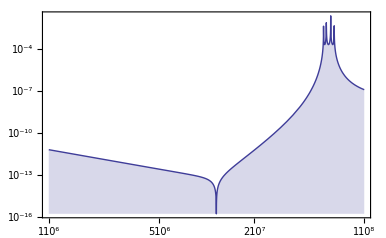

### Author

Jan G. Korvink © 2013

### Concept

This package facilitates the simulation of two-port networks. The design philosophy is as follows:

Specify: a circuit is specified using custom Mathematica heads. There are heads for primitive circuit elements such as resistors, inductances and capacitances, and combinations of elements in series or parallel, all of which are called objects. The primitive circuit elements are used to specify two-ports. Further specifications allow the interconnection of two-ports into circuits.


Verify: a circuit is checked for correctness by plotting it with the function CircuitGraphics[], which can handle two-ports as well as interconnections of two-ports.

Compute: a circuit can be converted into an expression using the function CircuitExpression[]. Different representations are possible.

Manipulate: conversions are possible between various representations of the two-ports. Also, methodology is provided to generate two-ports from nodal analysis models.

Analyse: a circuit can be simulated.

Complement: for example, the impedance matching network of a circuit can be computed.

Embed: a circuit can be embedded in another representation.

### Usage

This gets the package:
<<”~korvink/Twoport.m”

This lists the functions:
Names[“Twoport`*”]

### Todo features list:

+ How to make a balanced ABCD system? How to place items in the lower axis, so to speak?
+ Sources
+ Noise models
+ Stripline, and Cable twoport
+ Arbitrary networks
+ Circuit operators
+ Tidy up amplitude and phase
+ Netlist generation
+ Fixed size text in graphics (Scaled[] refers to the the entire plot range! Font size to the screen.
+ Plots: Nyquist (Transfer function, Im[] vs Re[], ω as parameter), Bode (dB of Power vs ω), Smith (Impedance Im[] vs Re[]), Root locus or Evans, Nichols or Black (|G(s)| vs Arg[G(s)]

Done:
+ Import 2 port models
+ Transistors
+ Smart evaluation and plotting of S-parameters.
+ Coupled inductor twoport (NO PLOT!)
+ Waveguide. 
+ Many conversions are missing.
+ Are the S-parameter conversions correctly implemented?

### References

1. Charles A. Desoer and Ernest S. Kuh, Basic Circuit Theory, McGraw-Hill, 1966
2. Wilfried Weißgerber, Elektrotechnik für Ingenieure 3, Vieweg 19??
3. K. C. Gupta, Peter S. Hall (Editors), Analysis and Design of Integrated Circuit Antenna Modules, Wiley Interscience, 19??
4. http://en.wikipedia.org/wiki/Electronic_filter_topology

### The functions and their use

```mathematica
fileName=StringJoin[NotebookDirectory[],"TwoPort.m"];
Get[fileName]
```

## The systematic test examples

### Names of items

```mathematica
Names["Twoport`Oneport*"]
Names["Twoport`Impedance*"]
Names["Twoport`Twoport*"]
Names["Twoport`To*"]
Names["Twoport`Circuit*"]
Complement[Names["Twoport`*"],Names["Twoport`Oneport*"],Names["Twoport`Impedance*"],
Names["Twoport`Twoport*"],Names["Twoport`To*"],
Names["Twoport`Circuit*"]
]
```

{OneportC,OneportCImpedance,OneportConversionRules,OneportCS,OneportL,OneportLImpedance,OneportOpenStub,OneportOpenStubImpedance,OneportParallel,OneportParallelImpedance,OneportR,OneportRImpedance,OneportSeries,OneportSeriesImpedance,OneportShortedStub,OneportShortedStubImpedance,OneportVS}

{}

{Twoport,TwoportBalancedLadder,TwoportBalancedLadderABCD,TwoportBoxsection,TwoportBoxsectionABCD,TwoportBridge,TwoportBridgeABCD,TwoportConversionRules,TwoportCoupledInductors,TwoportCoupledInductorsABCD,TwoportCsection,TwoportCsectionABCD,TwoportGammaI,TwoportGammaIABCD,TwoportGammaII,TwoportGammaIIABCD,TwoportGyrator,TwoportGyratorABCD,TwoportHsection,TwoportHsectionABCD,TwoportInvert,TwoportInvertABCD,TwoportLeftRight,TwoportLeftRightABCD,TwoportLossyWaveguide,TwoportLossyWaveguideABCD,TwoportMeasure,TwoportNMOScd,TwoportNMOScdABCD,TwoportNMOScg,TwoportNMOScgABCD,TwoportNMOScs,TwoportNMOScsABCD,TwoportNPNcb,TwoportNPNcbABCD,TwoportNPNcc,TwoportNPNccABCD,TwoportNPNce,TwoportNPNceABCD,TwoportPi,TwoportPiABCD,TwoportSeries,TwoportSeriesABCD,TwoportSeriesDown,TwoportSeriesDownABCD,TwoportShunt,TwoportShuntABCD,TwoportSwapTopBottom,TwoportTee,TwoportTeeABCD,TwoportTransformer,TwoportTransformerABCD,TwoportUnbalancedLadder,TwoportUnbalancedLadderABCD,TwoportWaveguide,TwoportWaveguideABCD,TwoportXsection,TwoportXsectionABCD,TwoportXsectionPi,TwoportXsectionPiABCD,TwoportXsectionTee,TwoportXsectionTeeABCD}

{ToA,ToB,ToH,ToP,ToS,ToT,Touchstone,ToY,ToZ}

{CircuitCascade,CircuitExpression,CircuitGraphics,CircuitHybrid,CircuitInverseHybrid,CircuitParallel,CircuitSerial}

{AllOneports,AllOneportsPattern,AllTwoportMatrices,AllTwoportMatricesPattern,AllTwoports,AllTwoportsPattern,Amplitude,Comment,CompleteTwoportMatrices,CompleteTwoportMatricesPattern,DrawCompound,DrawTwoport,ExtractTouchstoneNetwork,GridArrangement,JoinConversionRules,LogLinearPlotSparameters,matrixA,matrixB,MatrixFormat,matrixH,matrixP,matrixS,matrixT,matrixY,matrixZ,MixedModeOrder,NetworkData,NodalAdmittanceAssemble,NodalToTwoport,NodalY,NoiseData,NumberOfFrequencies,NumberOfNoiseFrequencies,NumberOfPorts,Optionline,Phase,PlotSparameters,PowerSolveABCD,ReadTouchstone,Reference,SmithPlot,SolveABCD,TwoPortDataOrder,UnwrapPhase,WriteTouchstone}

### Circuit specification and graphics

#### Circuit specification

```mathematica
testCircuitItems=
{TwoportShunt[OneportR[1]],
TwoportShunt[OneportL[1]],
TwoportShunt[OneportC[1]],
TwoportShunt[OneportShortedStub[1,1,1]],
TwoportShunt[OneportOpenStub[1,1,1]],

TwoportSeries[OneportR[1]],
TwoportSeries[OneportL[1]],
TwoportSeries[OneportC[1]],
TwoportSeries[OneportShortedStub[1,1,1]],
TwoportSeries[OneportOpenStub[1,1,1]],

TwoportSeriesDown[OneportR[1]],
TwoportSeriesDown[OneportL[1]],
TwoportSeriesDown[OneportC[1]],
TwoportSeriesDown[OneportShortedStub[1,1,1]],
TwoportSeriesDown[OneportOpenStub[1,1,1]],

TwoportLeftRight[OneportR[1],OneportL[1]],
TwoportLeftRight[OneportL[1],OneportR[1]],
TwoportLeftRight[OneportOpenStub[1],OneportShortedStub[1]],
TwoportLeftRight[OneportShortedStub[1],OneportOpenStub[1]],
TwoportLeftRight[OneportC[1],OneportC[1]],

TwoportGyrator[1],
TwoportGyrator[-1],
TwoportWaveguide[1,2,3],
TwoportTransformer[1],
TwoportInvert[],

TwoportPi[OneportR[1],OneportR[1],OneportR[1]],
TwoportPi[OneportL[1],OneportL[1],OneportL[1]],
TwoportPi[OneportC[1],OneportC[1],OneportC[1]],
TwoportPi[OneportOpenStub[1],OneportOpenStub[1],OneportOpenStub[1]],
TwoportPi[OneportShortedStub[1],OneportShortedStub[1],OneportShortedStub[1]],

TwoportTee[OneportR[1],OneportR[1],OneportR[1]],
TwoportTee[OneportL[1],OneportL[1],OneportL[1]],
TwoportTee[OneportC[1],OneportC[1],OneportC[1]],
TwoportTee[OneportOpenStub[1],OneportOpenStub[1],OneportOpenStub[1]],
TwoportTee[OneportShortedStub[1],OneportShortedStub[1],OneportShortedStub[1]],

TwoportGammaI[OneportR[1],OneportR[1]],
TwoportGammaI[OneportL[1],OneportL[1]],
TwoportGammaI[OneportC[1],OneportC[1]],
TwoportGammaI[OneportOpenStub[1],OneportOpenStub[1]],
TwoportGammaI[OneportShortedStub[1],OneportShortedStub[1]],

TwoportGammaII[OneportR[1],OneportR[1]],
TwoportGammaII[OneportL[1],OneportL[1]],
TwoportGammaII[OneportC[1],OneportC[1]],
TwoportGammaII[OneportOpenStub[1],OneportOpenStub[1]],
TwoportGammaII[OneportShortedStub[1],OneportShortedStub[1]],

TwoportCsection[OneportR[1],OneportR[1]],
TwoportCsection[OneportL[1],OneportL[1]],
TwoportCsection[OneportC[1],OneportC[1]],
TwoportCsection[OneportOpenStub[1],OneportOpenStub[1]],
TwoportCsection[OneportShortedStub[1],OneportShortedStub[1]],

TwoportHsection[OneportR[1],OneportR[1]],
TwoportHsection[OneportL[1],OneportL[1]],
TwoportHsection[OneportC[1],OneportC[1]],
TwoportHsection[OneportOpenStub[1],OneportOpenStub[1]],
TwoportHsection[OneportShortedStub[1],OneportShortedStub[1]],

TwoportBoxsection[OneportR[1],OneportR[1]],
TwoportBoxsection[OneportL[1],OneportL[1]],
TwoportBoxsection[OneportC[1],OneportC[1]],
TwoportBoxsection[OneportOpenStub[1],OneportOpenStub[1]],
TwoportBoxsection[OneportShortedStub[1],OneportShortedStub[1]],

TwoportXsection[OneportR[1],OneportR[1]],
TwoportXsection[OneportL[1],OneportL[1]],
TwoportXsection[OneportC[1],OneportC[1]],
TwoportXsection[OneportOpenStub[1],OneportOpenStub[1]],
TwoportXsection[OneportShortedStub[1],OneportShortedStub[1]],

TwoportBridge[OneportR[1],OneportR[1],OneportR[1],OneportR[1]],
TwoportBridge[OneportL[1],OneportL[1],OneportL[1],OneportL[1]],
TwoportBridge[OneportC[1],OneportC[1],OneportC[1],OneportC[1]],
TwoportBridge[OneportOpenStub[1],OneportOpenStub[1],OneportOpenStub[1],OneportOpenStub[1]],
TwoportBridge[OneportShortedStub[1],OneportShortedStub[1],OneportShortedStub[1],OneportShortedStub[1]],

TwoportUnbalancedLadder[OneportR[1]],
TwoportUnbalancedLadder[OneportL[1]],
TwoportUnbalancedLadder[OneportC[1]],
TwoportUnbalancedLadder[OneportShortedStub[1,1,1]],
TwoportUnbalancedLadder[OneportOpenStub[1,1,1]],

TwoportBalancedLadder[OneportR[1]],
TwoportBalancedLadder[OneportL[1]],
TwoportBalancedLadder[OneportC[1]],
TwoportBalancedLadder[OneportShortedStub[1,1,1]],
TwoportBalancedLadder[OneportOpenStub[1,1,1]],

TwoportXsectionTee[OneportR[1]],
TwoportXsectionTee[OneportL[1]],
TwoportXsectionTee[OneportC[1]],
TwoportXsectionTee[OneportShortedStub[1,1,1]],
TwoportXsectionTee[OneportOpenStub[1,1,1]],

TwoportXsectionPi[OneportR[1]],
TwoportXsectionPi[OneportL[1]],
TwoportXsectionPi[OneportC[1]],
TwoportXsectionPi[OneportShortedStub[1,1,1]],
TwoportXsectionPi[OneportOpenStub[1,1,1]],

TwoportNPNce[1,1,1],
TwoportNPNcb[1,1,1],
TwoportNPNcc[1,1,1],
TwoportInvert[],
TwoportInvert[],

TwoportNMOScs[1,1,1],
TwoportNMOScg[1,1,1],
TwoportNMOScd[1,1,1],
TwoportInvert[],
TwoportInvert[]

}
```

{TwoportShunt[OneportR[1]],TwoportShunt[OneportL[1]],TwoportShunt[OneportC[1]],TwoportShunt[OneportShortedStub[1,1,1]],TwoportShunt[OneportOpenStub[1,1,1]],TwoportSeries[OneportR[1]],TwoportSeries[OneportL[1]],TwoportSeries[OneportC[1]],TwoportSeries[OneportShortedStub[1,1,1]],TwoportSeries[OneportOpenStub[1,1,1]],TwoportSeriesDown[OneportR[1]],TwoportSeriesDown[OneportL[1]],TwoportSeriesDown[OneportC[1]],TwoportSeriesDown[OneportShortedStub[1,1,1]],TwoportSeriesDown[OneportOpenStub[1,1,1]],TwoportLeftRight[OneportR[1],OneportL[1]],TwoportLeftRight[OneportL[1],OneportR[1]],TwoportLeftRight[OneportOpenStub[1],OneportShortedStub[1]],TwoportLeftRight[OneportShortedStub[1],OneportOpenStub[1]],TwoportLeftRight[OneportC[1],OneportC[1]],TwoportGyrator[1],TwoportGyrator[-1],TwoportWaveguide[1,2,3],TwoportTransformer[1],TwoportInvert[],TwoportPi[OneportR[1],OneportR[1],OneportR[1]],TwoportPi[OneportL[1],OneportL[1],OneportL[1]],TwoportPi[OneportC[1],OneportC[1],OneportC[1]],TwoportPi[OneportOpenStub[1],OneportOpenStub[1],OneportOpenStub[1]],TwoportPi[OneportShortedStub[1],OneportShortedStub[1],OneportShortedStub[1]],TwoportTee[OneportR[1],OneportR[1],OneportR[1]],TwoportTee[OneportL[1],OneportL[1],OneportL[1]],TwoportTee[OneportC[1],OneportC[1],OneportC[1]],TwoportTee[OneportOpenStub[1],OneportOpenStub[1],OneportOpenStub[1]],TwoportTee[OneportShortedStub[1],OneportShortedStub[1],OneportShortedStub[1]],TwoportGammaI[OneportR[1],OneportR[1]],TwoportGammaI[OneportL[1],OneportL[1]],TwoportGammaI[OneportC[1],OneportC[1]],TwoportGammaI[OneportOpenStub[1],OneportOpenStub[1]],TwoportGammaI[OneportShortedStub[1],OneportShortedStub[1]],TwoportGammaII[OneportR[1],OneportR[1]],TwoportGammaII[OneportL[1],OneportL[1]],TwoportGammaII[OneportC[1],OneportC[1]],TwoportGammaII[OneportOpenStub[1],OneportOpenStub[1]],TwoportGammaII[OneportShortedStub[1],OneportShortedStub[1]],TwoportCsection[OneportR[1],OneportR[1]],TwoportCsection[OneportL[1],OneportL[1]],TwoportCsection[OneportC[1],OneportC[1]],TwoportCsection[OneportOpenStub[1],OneportOpenStub[1]],TwoportCsection[OneportShortedStub[1],OneportShortedStub[1]],TwoportHsection[OneportR[1],OneportR[1]],TwoportHsection[OneportL[1],OneportL[1]],TwoportHsection[OneportC[1],OneportC[1]],TwoportHsection[OneportOpenStub[1],OneportOpenStub[1]],TwoportHsection[OneportShortedStub[1],OneportShortedStub[1]],TwoportBoxsection[OneportR[1],OneportR[1]],TwoportBoxsection[OneportL[1],OneportL[1]],TwoportBoxsection[OneportC[1],OneportC[1]],TwoportBoxsection[OneportOpenStub[1],OneportOpenStub[1]],TwoportBoxsection[OneportShortedStub[1],OneportShortedStub[1]],TwoportXsection[OneportR[1],OneportR[1]],TwoportXsection[OneportL[1],OneportL[1]],TwoportXsection[OneportC[1],OneportC[1]],TwoportXsection[OneportOpenStub[1],OneportOpenStub[1]],TwoportXsection[OneportShortedStub[1],OneportShortedStub[1]],TwoportBridge[OneportR[1],OneportR[1],OneportR[1],OneportR[1]],TwoportBridge[OneportL[1],OneportL[1],OneportL[1],OneportL[1]],TwoportBridge[OneportC[1],OneportC[1],OneportC[1],OneportC[1]],TwoportBridge[OneportOpenStub[1],OneportOpenStub[1],OneportOpenStub[1],OneportOpenStub[1]],TwoportBridge[OneportShortedStub[1],OneportShortedStub[1],OneportShortedStub[1],OneportShortedStub[1]],TwoportUnbalancedLadder[OneportR[1]],TwoportUnbalancedLadder[OneportL[1]],TwoportUnbalancedLadder[OneportC[1]],TwoportUnbalancedLadder[OneportShortedStub[1,1,1]],TwoportUnbalancedLadder[OneportOpenStub[1,1,1]],TwoportBalancedLadder[OneportR[1]],TwoportBalancedLadder[OneportL[1]],TwoportBalancedLadder[OneportC[1]],TwoportBalancedLadder[OneportShortedStub[1,1,1]],TwoportBalancedLadder[OneportOpenStub[1,1,1]],TwoportXsectionTee[OneportR[1]],TwoportXsectionTee[OneportL[1]],TwoportXsectionTee[OneportC[1]],TwoportXsectionTee[OneportShortedStub[1,1,1]],TwoportXsectionTee[OneportOpenStub[1,1,1]],TwoportXsectionPi[OneportR[1]],TwoportXsectionPi[OneportL[1]],TwoportXsectionPi[OneportC[1]],TwoportXsectionPi[OneportShortedStub[1,1,1]],TwoportXsectionPi[OneportOpenStub[1,1,1]],TwoportNPNce[1,1,1],TwoportNPNcb[1,1,1],TwoportNPNcc[1,1,1],TwoportInvert[],TwoportInvert[],TwoportNMOScs[1,1,1],TwoportNMOScg[1,1,1],TwoportNMOScd[1,1,1],TwoportInvert[],TwoportInvert[]}

```mathematica
testCircuitInterconnections={
CircuitInverseHybrid[CircuitHybrid[CircuitCascade[CircuitParallel[TwoportSeries[OneportSeries[OneportC[c1],OneportR[r1]]],TwoportTransformer[1]] ,TwoportShunt[OneportL[l1]]] ,TwoportShunt[OneportL[l1]]] ,TwoportShunt[OneportL[l1]]],

CircuitHybrid[CircuitHybrid[CircuitHybrid[CircuitHybrid[TwoportSeries[OneportSeries[OneportC[c1],OneportR[r1]]],TwoportTransformer[1]] ,TwoportShunt[OneportL[l1]]] ,TwoportShunt[OneportL[l1]]] ,TwoportShunt[OneportL[l1]]],

CircuitParallel[CircuitParallel[CircuitParallel[CircuitParallel[TwoportSeries[OneportSeries[OneportC[c1],OneportR[r1]]],TwoportTransformer[1]] ,TwoportShunt[OneportL[l1]]] ,TwoportShunt[OneportL[l1]]] ,TwoportShunt[OneportL[l1]]],

CircuitSerial[CircuitSerial[CircuitSerial[CircuitSerial[TwoportSeries[OneportSeries[OneportC[c1],OneportR[r1]]],TwoportTransformer[1]] ,TwoportShunt[OneportL[l1]]] ,TwoportShunt[OneportL[l1]]] ,TwoportShunt[OneportL[l1]]],

CircuitCascade[CircuitCascade[CircuitCascade[CircuitCascade[TwoportSeries[OneportSeries[OneportC[c1],OneportR[r1]]],TwoportTransformer[1]] ,TwoportShunt[OneportL[l1]]] ,TwoportShunt[OneportL[l1]]] ,TwoportShunt[OneportL[l1]]],

CircuitSerial[CircuitSerial[CircuitSerial[CircuitSerial[TwoportSeries[OneportSeries[OneportC[c1],OneportR[r1]]],TwoportTransformer[1]] ,TwoportShunt[OneportL[l1]]] ,TwoportShunt[OneportL[l1]]] ,TwoportShunt[OneportL[l1]]]
}
```

{CircuitInverseHybrid[CircuitHybrid[CircuitCascade[CircuitParallel[TwoportSeries[OneportSeries[OneportC[c1],OneportR[r1]]],TwoportTransformer[1]],TwoportShunt[OneportL[l1]]],TwoportShunt[OneportL[l1]]],TwoportShunt[OneportL[l1]]],CircuitHybrid[CircuitHybrid[CircuitHybrid[CircuitHybrid[TwoportSeries[OneportSeries[OneportC[c1],OneportR[r1]]],TwoportTransformer[1]],TwoportShunt[OneportL[l1]]],TwoportShunt[OneportL[l1]]],TwoportShunt[OneportL[l1]]],CircuitParallel[CircuitParallel[CircuitParallel[CircuitParallel[TwoportSeries[OneportSeries[OneportC[c1],OneportR[r1]]],TwoportTransformer[1]],TwoportShunt[OneportL[l1]]],TwoportShunt[OneportL[l1]]],TwoportShunt[OneportL[l1]]],CircuitSerial[CircuitSerial[CircuitSerial[CircuitSerial[TwoportSeries[OneportSeries[OneportC[c1],OneportR[r1]]],TwoportTransformer[1]],TwoportShunt[OneportL[l1]]],TwoportShunt[OneportL[l1]]],TwoportShunt[OneportL[l1]]],CircuitCascade[CircuitCascade[CircuitCascade[CircuitCascade[TwoportSeries[OneportSeries[OneportC[c1],OneportR[r1]]],TwoportTransformer[1]],TwoportShunt[OneportL[l1]]],TwoportShunt[OneportL[l1]]],TwoportShunt[OneportL[l1]]],CircuitSerial[CircuitSerial[CircuitSerial[CircuitSerial[TwoportSeries[OneportSeries[OneportC[c1],OneportR[r1]]],TwoportTransformer[1]],TwoportShunt[OneportL[l1]]],TwoportShunt[OneportL[l1]]],TwoportShunt[OneportL[l1]]]}

#### Circuit graphics

```mathematica
GraphicsGrid[Partition[CircuitGraphics[#]&/@testCircuitItems,5]]
```

-Graphics-

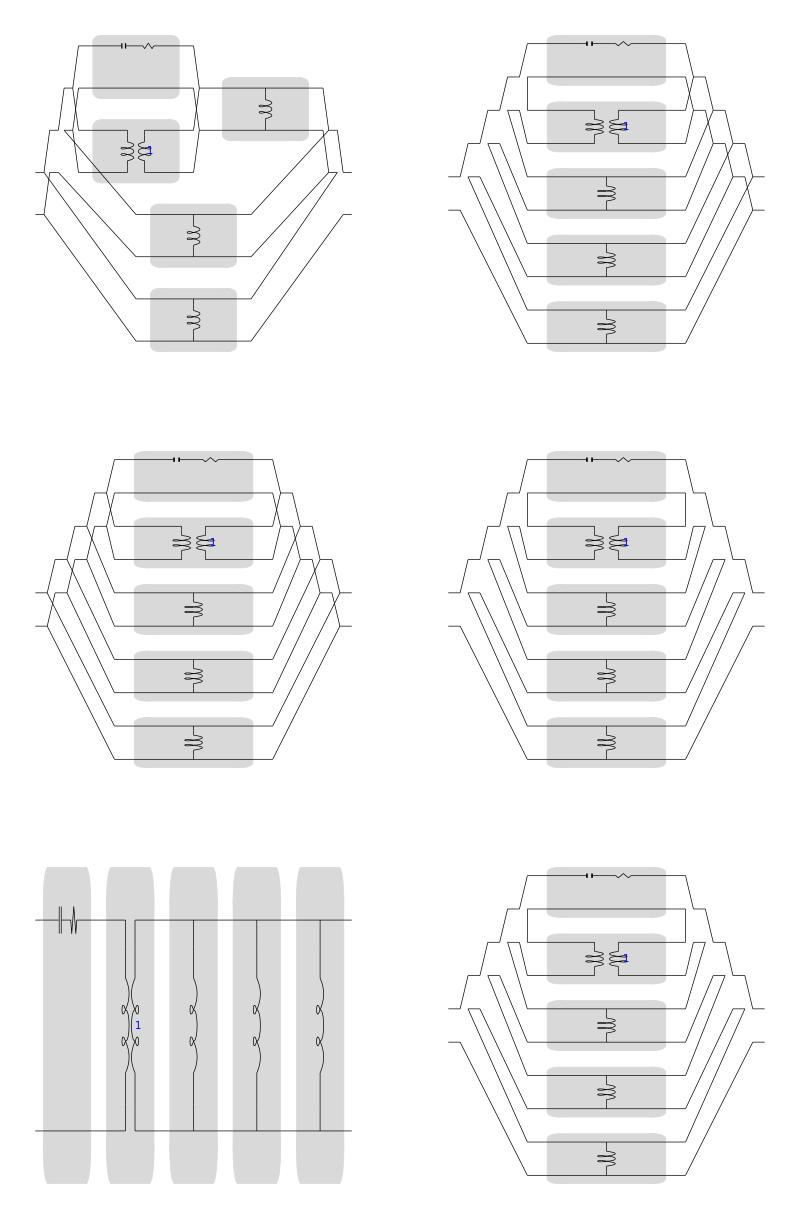

```mathematica
GraphicsGrid[Partition[CircuitGraphics[#]&/@testCircuitInterconnections,2]]
```

### Conversions among matrix representations

#### Basic test

```mathematica
Clear[k11,k12,k21,k22]

ToA[#[{k11,k12},{k21,k22}]]&/@CompleteTwoportMatrices
ToB[#[{k11,k12},{k21,k22}]]&/@CompleteTwoportMatrices
ToZ[#[{k11,k12},{k21,k22}]]&/@CompleteTwoportMatrices
ToY[#[{k11,k12},{k21,k22}]]&/@CompleteTwoportMatrices
ToH[#[{k11,k12},{k21,k22}]]&/@CompleteTwoportMatrices
ToP[#[{k11,k12},{k21,k22}]]&/@CompleteTwoportMatrices
ToS[#[{k11,k12},{k21,k22}]]&/@CompleteTwoportMatrices
```

{^A{{k11,k12},{k21,k22}},^A{{k22/(-k12 k21+k11 k22),k12/(k12 k21-k11 k22)},{k21/(k12 k21-k11 k22),k11/(-k12 k21+k11 k22)}},^A{{k11/k21,k12-(k11 k22)/k21},{1/k21,-k22/k21}},^A{{-k22/k21,1/k21},{k12-(k11 k22)/k21,k11/k21}},^A{{k12-(k11 k22)/k21,k11/k21},{-k22/k21,1/k21}},^A{{1/k21,-k22/k21},{k11/k21,k12-(k11 k22)/k21}},^A{{(k12 k21+(1+k11) (1-k22))/(2 k21),(25 (-k12 k21+(1+k11) (1+k22)))/k21},{(-k12 k21+(1-k11) (1-k22))/(100 k21),(k12 k21+(1-k11) (1+k22))/(2 k21)}},^A{{-1/(2 k21)(-k12 k21+k11 k22) ((k12 k21)/(-k12 k21+k11 k22)^2+(1-k11/(-k12 k21+k11 k22)) (1+k22/(-k12 k21+k11 k22))),-1/k21 25 (-k12 k21+k11 k22) (-(k12 k21)/(-k12 k21+k11 k22)^2+(1+k11/(-k12 k21+k11 k22)) (1+k22/(-k12 k21+k11 k22)))},{-1/(100 k21)(-k12 k21+k11 k22) (-(k12 k21)/(-k12 k21+k11 k22)^2+(1-k11/(-k12 k21+k11 k22)) (1-k22/(-k12 k21+k11 k22))),-1/(2 k21)(-k12 k21+k11 k22) ((k12 k21)/(-k12 k21+k11 k22)^2+(1+k11/(-k12 k21+k11 k22)) (1-k22/(-k12 k21+k11 k22)))}}}

{^B{{k22/(-k12 k21+k11 k22),k12/(k12 k21-k11 k22)},{k21/(k12 k21-k11 k22),k11/(-k12 k21+k11 k22)}},^B{{k11,k12},{k21,k22}},^B{{k22/k12,k21-(k11 k22)/k12},{1/k12,-k11/k12}},^B{{-k11/k12,1/k12},{k21-(k11 k22)/k12,k22/k12}},^B{{1/k12,-k11/k12},{k22/k12,k21-(k11 k22)/k12}},^B{{k21-(k11 k22)/k12,k22/k12},{-k11/k12,1/k12}},^B{{(1+k12 k21+k22-k11 (1+k22))/(2 k12),-(25 (1+k11-k12 k21+k22+k11 k22))/k12},{(-1+k11+k12 k21+k22-k11 k22)/(100 k12),(1+k11+k12 k21-k22-k11 k22)/(2 k12)}},^B{{(1+k12 k21+k22-k11 (1+k22))/(2 k12),(25 (1+k11-k12 k21+k22+k11 k22))/k12},{-(-1+k11+k12 k21+k22-k11 k22)/(100 k12),(1+k11+k12 k21-k22-k11 k22)/(2 k12)}}}

{^Z{{k11/k21,k12-(k11 k22)/k21},{1/k21,-k22/k21}},^Z{{-k22/k21,1/k21},{k12-(k11 k22)/k21,k11/k21}},^Z{{k11,k12},{k21,k22}},^Z{{k22/(-k12 k21+k11 k22),k12/(k12 k21-k11 k22)},{k21/(k12 k21-k11 k22),k11/(-k12 k21+k11 k22)}},^Z{{k11-(k12 k21)/k22,k12/k22},{-k21/k22,1/k22}},^Z{{1/k11,-k12/k11},{k21/k11,-(k12 k21)/k11+k22}},^Z{{-(50 (1+k11+k12 k21-k22-k11 k22))/(-1+k11+k12 k21+k22-k11 k22),(100 k12)/(-1+k11+k12 k21+k22-k11 k22)},{-(100 k21)/(-1+k11+k12 k21+k22-k11 k22),(50 (1+k12 k21+k22-k11 (1+k22)))/(-1+k11+k12 k21+k22-k11 k22)}},^Z{{(50 (1+k11+k12 k21-k22-k11 k22))/(-1+k11+k12 k21+k22-k11 k22),-(100 k12)/(-1+k11+k12 k21+k22-k11 k22)},{(100 k21)/(-1+k11+k12 k21+k22-k11 k22),-(50 (1+k12 k21+k22-k11 (1+k22)))/(-1+k11+k12 k21+k22-k11 k22)}}}

{^Y{{k22/k12,k21-(k11 k22)/k12},{1/k12,-k11/k12}},^Y{{-k11/k12,1/k12},{k21-(k11 k22)/k12,k22/k12}},^Y{{k22/(-k12 k21+k11 k22),k12/(k12 k21-k11 k22)},{k21/(k12 k21-k11 k22),k11/(-k12 k21+k11 k22)}},^Y{{k11,k12},{k21,k22}},^Y{{1/k11,-k12/k11},{k21/k11,-(k12 k21)/k11+k22}},^Y{{k11-(k12 k21)/k22,k12/k22},{-k21/k22,1/k22}},^Y{{(1+k12 k21+k22-k11 (1+k22))/(50 (1+k11-k12 k21+k22+k11 k22)),-k12/(25 (1+k11-k12 k21+k22+k11 k22))},{k21/(25 (1+k11-k12 k21+k22+k11 k22)),(-1-k12 k21+k11 (-1+k22)+k22)/(50 (1+k11-k12 k21+k22+k11 k22))}},^Y{{(-1+k11-k12 k21-k22+k11 k22)/(50 (1+k11-k12 k21+k22+k11 k22)),k12/(25 (1+k11-k12 k21+k22+k11 k22))},{-k21/(25 (1+k11-k12 k21+k22+k11 k22)),(1+k11+k12 k21-k22-k11 k22)/(50 (1+k11-k12 k21+k22+k11 k22))}}}

{^H{{k12/k22,k11-(k12 k21)/k22},{1/k22,-k21/k22}},^H{{-k12/k11,1/k11},{-(k12 k21)/k11+k22,k21/k11}},^H{{k11-(k12 k21)/k22,k12/k22},{-k21/k22,1/k22}},^H{{1/k11,-k12/k11},{k21/k11,-(k12 k21)/k11+k22}},^H{{k11,k12},{k21,k22}},^H{{k22/(-k12 k21+k11 k22),k12/(k12 k21-k11 k22)},{k21/(k12 k21-k11 k22),k11/(-k12 k21+k11 k22)}},^H{{(50 (1+k11-k12 k21+k22+k11 k22))/(1+k12 k21+k22-k11 (1+k22)),(2 k12)/(1+k12 k21+k22-k11 (1+k22))},{(2 k21)/(1+k12 k21+k22-k11 (1+k22)),-(-1+k11+k12 k21+k22-k11 k22)/(50 (-1+k11-k12 k21-k22+k11 k22))}},^H{{(50 (1+k11-k12 k21+k22+k11 k22))/(-1+k11-k12 k21-k22+k11 k22),(2 k12)/(1+k12 k21+k22-k11 (1+k22))},{(2 k21)/(1+k12 k21+k22-k11 (1+k22)),(-1+k11+k12 k21+k22-k11 k22)/(50 (-1+k11-k12 k21-k22+k11 k22))}}}

{^P{{k21/k11,-(k12 k21)/k11+k22},{1/k11,-k12/k11}},^P{{-k21/k22,1/k22},{k11-(k12 k21)/k22,k12/k22}},^P{{1/k11,-k12/k11},{k21/k11,-(k12 k21)/k11+k22}},^P{{k11-(k12 k21)/k22,k12/k22},{-k21/k22,1/k22}},^P{{k22/(-k12 k21+k11 k22),k12/(k12 k21-k11 k22)},{k21/(k12 k21-k11 k22),k11/(-k12 k21+k11 k22)}},^P{{k11,k12},{k21,k22}},^P{{(-1+k11+k12 k21+k22-k11 k22)/(50 (-1-k12 k21+k11 (-1+k22)+k22)),(2 k12)/(1+k11+k12 k21-k22-k11 k22)},{(2 k21)/(k12 k21-(1+k11) (-1+k22)),-(50 (1+k11-k12 k21+k22+k11 k22))/(k12 k21-(1+k11) (-1+k22))}},^P{{-(-1+k11+k12 k21+k22-k11 k22)/(50 (-1-k12 k21+k11 (-1+k22)+k22)),(2 k12)/(1+k11+k12 k21-k22-k11 k22)},{(2 k21)/(1+k11+k12 k21-k22-k11 k22),(50 (1+k11-k12 k21+k22+k11 k22))/(1+k11+k12 k21-k22-k11 k22)}}}

{^S{{(k11+k12/50-50 k21-k22)/(k11+k12/50+50 k21+k22),(2 (-k12 k21+k11 k22))/(k11+k12/50+50 k21+k22)},{2/(k11+k12/50+50 k21+k22),(-k11+k12/50-50 k21+k22)/(k11+k12/50+50 k21+k22)}},^S{{(k12/(50 (k12 k21-k11 k22))-(50 k21)/(k12 k21-k11 k22)-k11/(-k12 k21+k11 k22)+k22/(-k12 k21+k11 k22))/(k12/(50 (k12 k21-k11 k22))+(50 k21)/(k12 k21-k11 k22)+k11/(-k12 k21+k11 k22)+k22/(-k12 k21+k11 k22)),(2 (-(k12 k21)/(k12 k21-k11 k22)^2+(k11 k22)/(-k12 k21+k11 k22)^2))/(k12/(50 (k12 k21-k11 k22))+(50 k21)/(k12 k21-k11 k22)+k11/(-k12 k21+k11 k22)+k22/(-k12 k21+k11 k22))},{2/(k12/(50 (k12 k21-k11 k22))+(50 k21)/(k12 k21-k11 k22)+k11/(-k12 k21+k11 k22)+k22/(-k12 k21+k11 k22)),(k12/(50 (k12 k21-k11 k22))-(50 k21)/(k12 k21-k11 k22)+k11/(-k12 k21+k11 k22)-k22/(-k12 k21+k11 k22))/(k12/(50 (k12 k21-k11 k22))+(50 k21)/(k12 k21-k11 k22)+k11/(-k12 k21+k11 k22)+k22/(-k12 k21+k11 k22))}},^S{{(-50/k21+k11/k21+k22/k21+1/50 (k12-(k11 k22)/k21))/(50/k21+k11/k21-k22/k21+1/50 (k12-(k11 k22)/k21)),(2 (-(k11 k22)/k21^2-(k12-(k11 k22)/k21)/k21))/(50/k21+k11/k21-k22/k21+1/50 (k12-(k11 k22)/k21))},{2/(50/k21+k11/k21-k22/k21+1/50 (k12-(k11 k22)/k21)),(-50/k21-k11/k21-k22/k21+1/50 (k12-(k11 k22)/k21))/(50/k21+k11/k21-k22/k21+1/50 (k12-(k11 k22)/k21))}},^S{{(1/(50 k21)-k11/k21-k22/k21-50 (k12-(k11 k22)/k21))/(1/(50 k21)+k11/k21-k22/k21+50 (k12-(k11 k22)/k21)),(2 (-(k11 k22)/k21^2-(k12-(k11 k22)/k21)/k21))/(1/(50 k21)+k11/k21-k22/k21+50 (k12-(k11 k22)/k21))},{2/(1/(50 k21)+k11/k21-k22/k21+50 (k12-(k11 k22)/k21)),(1/(50 k21)+k11/k21+k22/k21-50 (k12-(k11 k22)/k21))/(1/(50 k21)+k11/k21-k22/k21+50 (k12-(k11 k22)/k21))}},^S{{(k12-1/k21+k11/(50 k21)+(50 k22)/k21-(k11 k22)/k21)/(k12+1/k21+k11/(50 k21)-(50 k22)/k21-(k11 k22)/k21),(2 ((k11 k22)/k21^2+(k12-(k11 k22)/k21)/k21))/(k12+1/k21+k11/(50 k21)-(50 k22)/k21-(k11 k22)/k21)},{2/(k12+1/k21+k11/(50 k21)-(50 k22)/k21-(k11 k22)/k21),(-k12+1/k21+k11/(50 k21)+(50 k22)/k21+(k11 k22)/k21)/(k12+1/k21+k11/(50 k21)-(50 k22)/k21-(k11 k22)/k21)}},^S{{(-k12+1/k21-(50 k11)/k21-k22/(50 k21)+(k11 k22)/k21)/(k12+1/k21+(50 k11)/k21-k22/(50 k21)-(k11 k22)/k21),(2 ((k11 k22)/k21^2+(k12-(k11 k22)/k21)/k21))/(k12+1/k21+(50 k11)/k21-k22/(50 k21)-(k11 k22)/k21)},{2/(k12+1/k21+(50 k11)/k21-k22/(50 k21)-(k11 k22)/k21),(k12-1/k21-(50 k11)/k21-k22/(50 k21)-(k11 k22)/k21)/(k12+1/k21+(50 k11)/k21-k22/(50 k21)-(k11 k22)/k21)}},^S{{k11,k12},{k21,k22}},^S{{k22/(-k12 k21+k11 k22),-k12/(-k12 k21+k11 k22)},{-k21/(-k12 k21+k11 k22),k11/(-k12 k21+k11 k22)}}}

#### Truth test for the normal twoports

```mathematica
Clear[m,m1,m2,k11,k12,k21,k22]

m=matrixA[{k11,k12},{k21,k22}];
{ToA[ToA[m]]===m,
ToA[ToB[m]]===m,
ToA[ToZ[m]]===m,
ToA[ToY[m]]===m,
ToA[ToH[m]]===m,
ToA[ToP[m]]===m 
}
m=matrixB[{k11,k12},{k21,k22}];
{ToB[ToA[m]]===m,
ToB[ToB[m]]===m,
ToB[ToZ[m]]===m,
ToB[ToY[m]]===m,
ToB[ToH[m]]===m,
ToB[ToP[m]]===m
}
m=matrixZ[{k11,k12},{k21,k22}];
{ToZ[ToA[m]]===m,
ToZ[ToB[m]]===m,
ToZ[ToZ[m]]===m,
ToZ[ToY[m]]===m,
ToZ[ToH[m]]===m,
ToZ[ToP[m]]===m
}
m=matrixY[{k11,k12},{k21,k22}];
{ToY[ToA[m]]===m,
ToY[ToB[m]]===m,
ToY[ToZ[m]]===m,
ToY[ToY[m]]===m,
ToY[ToH[m]]===m,
ToY[ToP[m]]===m
}
m=matrixH[{k11,k12},{k21,k22}];
{ToH[ToA[m]]===m,
ToH[ToB[m]]===m,
ToH[ToZ[m]]===m,
ToH[ToY[m]]===m,
ToH[ToH[m]]===m,
ToH[ToP[m]]===m
}
m=matrixP[{k11,k12},{k21,k22}];
{ToP[ToA[m]]===m,
ToP[ToB[m]]===m,
ToP[ToZ[m]]===m,
ToP[ToY[m]]===m,
ToP[ToH[m]]===m,
ToP[ToP[m]]===m
}
```

{True,True,True,True,True,True}

{True,True,True,True,True,True}

{True,True,True,True,True,True}

«3 more identical outputs»

#### Truth test for the S and T matrices

I have had to add some tricks to get by the symbolic processing.

```mathematica
Clear[m,m1,m2,k11,k12,k21,k22]

m=matrixA[{k11,k12},{k21,k22}];
m1=(ToA[ToS[m]])/.{k11->1,k12->π,k21->E,k22->E ^π}//Simplify;
m2=(ToA[ToT[m]])/.{k11->1,k12->π,k21->E,k22->E ^π}//Simplify;
{m1===(m/.{k11->1,k12->π,k21->E,k22->E ^π}),
m2===(m/.{k11->1,k12->π,k21->E,k22->E ^π})
}
m=matrixB[{k11,k12},{k21,k22}];
{ToB[ToS[m]]===m,
ToB[ToT[m]]===m
}
m=matrixZ[{k11,k12},{k21,k22}];
{ToZ[ToS[m]]===m,
ToZ[ToT[m]]===m
}
m=matrixY[{k11,k12},{k21,k22}];
{ToY[ToS[m]]===m,
ToY[ToT[m]]===m
}
m=matrixH[{k11,k12},{k21,k22}];
{ToH[ToS[m]]===m,
ToH[ToT[m]]===m
}
m=matrixP[{k11,k12},{k21,k22}];
{ToP[ToS[m]]===m,
ToP[ToT[m]]===m
}
m=matrixS[{k11,k12},{k21,k22}];
m1=(ToS[ToS[m]])/.{k11->1,k12->π,k21->E,k22->E ^π}//Simplify;
m2=(ToS[ToT[m]])/.{k11->1,k12->π,k21->E,k22->E ^π}//Simplify;
{m1===(m/.{k11->1,k12->π,k21->E,k22->E ^π}),
m2===(m/.{k11->1,k12->π,k21->E,k22->E ^π})
}
m=matrixT[{k11,k12},{k21,k22}];
m1=(ToT[ToS[m]])/.{k11->1,k12->π,k21->E,k22->E ^π}//Simplify;
m2=(ToT[ToT[m]])/.{k11->1,k12->π,k21->E,k22->E ^π}//Simplify;
{m1===(m/.{k11->1,k12->π,k21->E,k22->E ^π}),
m2===(m/.{k11->1,k12->π,k21->E,k22->E ^π})
}
```

### The twoport matrices

```mathematica
Clear[z,z1,z2,z3,r1,r2,α,β,γ,l,n,m,rbe,b,yce,ygs,gm,yds]
TwoportSeriesABCD[z]
TwoportSeriesDownABCD[z]
TwoportShuntABCD[z]
TwoportLeftRightABCD[z1,z2]
TwoportGyratorABCD[α]
TwoportInvertABCD[]
TwoportWaveguideABCD[z0,β,l]
TwoportLossyWaveguideABCD[z0,γ,l]
TwoportTransformerABCD[n]
TwoportPiABCD[z1,z2,z3]
TwoportTeeABCD[z1,z2,z3]
TwoportGammaIABCD[z1,z2]
TwoportGammaIIABCD[z1,z2]
TwoportUnbalancedLadderABCD[z1,z2,n]
TwoportCoupledInductorsABCD[z1,z2,n]
TwoportCsectionABCD[z1,z2]
TwoportHsectionABCD[z1,z2]
TwoportBoxsectionABCD[z1,z2]
TwoportXsectionABCD[z1,z2]
TwoportBalancedLadderABCD[z1,z2,n]
TwoportXsectionTeeABCD[z]
TwoportXsectionPiABCD[z1,z2]
TwoportBridgeABCD[z1,z2,r1,r2]

TwoportNPNceABCD[rbe,b,yce]
TwoportNPNcbABCD[rbe,b,yce]
TwoportNPNccABCD[rbe,b,yce]

TwoportNMOScsABCD[ygs,gm,yds]
TwoportNMOScgABCD[ygs,gm,yds]
TwoportNMOScdABCD[ygs,gm,yds]
```

^A{{1,z},{0,1}}

^A{{1,-z},{0,1}}

^A{{1,0},{1/z,1}}

^A{{z1,0},{0,z2}}

^A{{0,α},{-1/α,0}}

^A{{0,1},{1,0}}

^A{{Cos[l β],ⅈ z0 Sin[l β]},{(ⅈ Sin[l β])/z0,Cos[l β]}}

^A{{Cosh[l γ],ⅈ z0 Sinh[l γ]},{(ⅈ Sinh[l γ])/z0,Cosh[l γ]}}

^A{{n,0},{0,1/n}}

^A{{1+z2/z3,z2},{1/z1+(1+z2/z1)/z3,1+z2/z1}}

^A{{1+z1/z2,z1+(1+z1/z2) z3},{1/z2,1+z3/z2}}

^A{{1,z2},{1/z1,1+z2/z1}}

^A{{1+z1/z2,z1},{1/z2,1}}

^A{{(1+z1/(2 z2)) (-(2^-n (-z2-√z2 √(4 z1+z2)) ((2 z1+z2-√z2 √(4 z1+z2))/z1)^(-1+n))/(√z2 √(4 z1+z2))+(2^-n (-z2+√z2 √(4 z1+z2)) ((2 z1+z2+√z2 √(4 z1+z2))/z1)^(-1+n))/(√z2 √(4 z1+z2)))+z1 (-(2^-n z1 ((2 z1+z2-√z2 √(4 z1+z2))/z1)^n)/(√z2 √(4 z1+z2) (2 z1+z2-√z2 √(4 z1+z2)))+(2^-n z1 ((2 z1+z2+√z2 √(4 z1+z2))/z1)^n)/(√z2 √(4 z1+z2) (2 z1+z2+√z2 √(4 z1+z2))))+1/z2((1+z1/(2 z2)) (1/(√(4 z1+z2))2^-n (-√z2+√(4 z1+z2)) (-z2-√z2 √(4 z1+z2)) ((2 z1+z2-√z2 √(4 z1+z2))/z1)^(-1+n)+1/(√(4 z1+z2))2^-n (√z2+√(4 z1+z2)) (-z2+√z2 √(4 z1+z2)) ((2 z1+z2+√z2 √(4 z1+z2))/z1)^(-1+n))+z1 ((2^-n z1 (-√z2+√(4 z1+z2)) ((2 z1+z2-√z2 √(4 z1+z2))/z1)^n)/(√(4 z1+z2) (2 z1+z2-√z2 √(4 z1+z2)))+(2^-n z1 (√z2+√(4 z1+z2)) ((2 z1+z2+√z2 √(4 z1+z2))/z1)^n)/(√(4 z1+z2) (2 z1+z2+√z2 √(4 z1+z2))))+2 z1 ((1+z1/(2 z2)) (-(2^-n (-z2-√z2 √(4 z1+z2)) ((2 z1+z2-√z2 √(4 z1+z2))/z1)^(-1+n))/(√z2 √(4 z1+z2))+(2^-n (-z2+√z2 √(4 z1+z2)) ((2 z1+z2+√z2 √(4 z1+z2))/z1)^(-1+n))/(√z2 √(4 z1+z2)))+z1 (-(2^-n z1 ((2 z1+z2-√z2 √(4 z1+z2))/z1)^n)/(√z2 √(4 z1+z2) (2 z1+z2-√z2 √(4 z1+z2)))+(2^-n z1 ((2 z1+z2+√z2 √(4 z1+z2))/z1)^n)/(√z2 √(4 z1+z2) (2 z1+z2+√z2 √(4 z1+z2)))))),(1+z1/(2 z2)) (1/(√(4 z1+z2))2^-n (-√z2+√(4 z1+z2)) (-z2-√z2 √(4 z1+z2)) ((2 z1+z2-√z2 √(4 z1+z2))/z1)^(-1+n)+1/(√(4 z1+z2))2^-n (√z2+√(4 z1+z2)) (-z2+√z2 √(4 z1+z2)) ((2 z1+z2+√z2 √(4 z1+z2))/z1)^(-1+n))+z1 ((2^-n z1 (-√z2+√(4 z1+z2)) ((2 z1+z2-√z2 √(4 z1+z2))/z1)^n)/(√(4 z1+z2) (2 z1+z2-√z2 √(4 z1+z2)))+(2^-n z1 (√z2+√(4 z1+z2)) ((2 z1+z2+√z2 √(4 z1+z2))/z1)^n)/(√(4 z1+z2) (2 z1+z2+√z2 √(4 z1+z2))))+2 z1 ((1+z1/(2 z2)) (-(2^-n (-z2-√z2 √(4 z1+z2)) ((2 z1+z2-√z2 √(4 z1+z2))/z1)^(-1+n))/(√z2 √(4 z1+z2))+(2^-n (-z2+√z2 √(4 z1+z2)) ((2 z1+z2+√z2 √(4 z1+z2))/z1)^(-1+n))/(√z2 √(4 z1+z2)))+z1 (-(2^-n z1 ((2 z1+z2-√z2 √(4 z1+z2))/z1)^n)/(√z2 √(4 z1+z2) (2 z1+z2-√z2 √(4 z1+z2)))+(2^-n z1 ((2 z1+z2+√z2 √(4 z1+z2))/z1)^n)/(√z2 √(4 z1+z2) (2 z1+z2+√z2 √(4 z1+z2)))))},{-(2^-n z1 ((2 z1+z2-√z2 √(4 z1+z2))/z1)^n)/(√z2 √(4 z1+z2) (2 z1+z2-√z2 √(4 z1+z2)))+(2^-n z1 ((2 z1+z2+√z2 √(4 z1+z2))/z1)^n)/(√z2 √(4 z1+z2) (2 z1+z2+√z2 √(4 z1+z2)))+1/(2 z2)(-(2^-n (-z2-√z2 √(4 z1+z2)) ((2 z1+z2-√z2 √(4 z1+z2))/z1)^(-1+n))/(√z2 √(4 z1+z2))+(2^-n (-z2+√z2 √(4 z1+z2)) ((2 z1+z2+√z2 √(4 z1+z2))/z1)^(-1+n))/(√z2 √(4 z1+z2)))+1/z2((2^-n z1 (-√z2+√(4 z1+z2)) ((2 z1+z2-√z2 √(4 z1+z2))/z1)^n)/(√(4 z1+z2) (2 z1+z2-√z2 √(4 z1+z2)))+(2^-n z1 (√z2+√(4 z1+z2)) ((2 z1+z2+√z2 √(4 z1+z2))/z1)^n)/(√(4 z1+z2) (2 z1+z2+√z2 √(4 z1+z2)))+1/(2 z2)(1/(√(4 z1+z2))2^-n (-√z2+√(4 z1+z2)) (-z2-√z2 √(4 z1+z2)) ((2 z1+z2-√z2 √(4 z1+z2))/z1)^(-1+n)+1/(√(4 z1+z2))2^-n (√z2+√(4 z1+z2)) (-z2+√z2 √(4 z1+z2)) ((2 z1+z2+√z2 √(4 z1+z2))/z1)^(-1+n))+2 z1 (-(2^-n z1 ((2 z1+z2-√z2 √(4 z1+z2))/z1)^n)/(√z2 √(4 z1+z2) (2 z1+z2-√z2 √(4 z1+z2)))+(2^-n z1 ((2 z1+z2+√z2 √(4 z1+z2))/z1)^n)/(√z2 √(4 z1+z2) (2 z1+z2+√z2 √(4 z1+z2)))+1/(2 z2)(-(2^-n (-z2-√z2 √(4 z1+z2)) ((2 z1+z2-√z2 √(4 z1+z2))/z1)^(-1+n))/(√z2 √(4 z1+z2))+(2^-n (-z2+√z2 √(4 z1+z2)) ((2 z1+z2+√z2 √(4 z1+z2))/z1)^(-1+n))/(√z2 √(4 z1+z2))))),(2^-n z1 (-√z2+√(4 z1+z2)) ((2 z1+z2-√z2 √(4 z1+z2))/z1)^n)/(√(4 z1+z2) (2 z1+z2-√z2 √(4 z1+z2)))+(2^-n z1 (√z2+√(4 z1+z2)) ((2 z1+z2+√z2 √(4 z1+z2))/z1)^n)/(√(4 z1+z2) (2 z1+z2+√z2 √(4 z1+z2)))+1/(2 z2)(1/(√(4 z1+z2))2^-n (-√z2+√(4 z1+z2)) (-z2-√z2 √(4 z1+z2)) ((2 z1+z2-√z2 √(4 z1+z2))/z1)^(-1+n)+1/(√(4 z1+z2))2^-n (√z2+√(4 z1+z2)) (-z2+√z2 √(4 z1+z2)) ((2 z1+z2+√z2 √(4 z1+z2))/z1)^(-1+n))+2 z1 (-(2^-n z1 ((2 z1+z2-√z2 √(4 z1+z2))/z1)^n)/(√z2 √(4 z1+z2) (2 z1+z2-√z2 √(4 z1+z2)))+(2^-n z1 ((2 z1+z2+√z2 √(4 z1+z2))/z1)^n)/(√z2 √(4 z1+z2) (2 z1+z2+√z2 √(4 z1+z2)))+1/(2 z2)(-(2^-n (-z2-√z2 √(4 z1+z2)) ((2 z1+z2-√z2 √(4 z1+z2))/z1)^(-1+n))/(√z2 √(4 z1+z2))+(2^-n (-z2+√z2 √(4 z1+z2)) ((2 z1+z2+√z2 √(4 z1+z2))/z1)^(-1+n))/(√z2 √(4 z1+z2))))}}

^A{{1+(-n+z1)/n,-n+z1+(1+(-n+z1)/n) (-n+z2)},{1/n,1+(-n+z2)/n}}

^A{{1+z1/(2 z2),z1/2},{1/z2,1}}

^A{{1+z1/(2 z2),z1/2+1/2 z1 (1+z1/(2 z2))},{1/z2,1+z1/(2 z2)}}

^A{{1+z1/(2 z2),z1/2},{1/z2+(1+z1/(2 z2))/z2,1+z1/(2 z2)}}

^A{{(z1+z2)/(z1-z2),(2 z1 z2)/(z1-z2)},{2/(z1-z2),(z1+z2)/(z1-z2)}}

^A{{1,0},{0,1}}

^A{{1,0},{0,1}}

^A{{1,0},{0,1}}

^A{{((r1+r2) (z1+z2))/(-r2 z1+r1 z2),(r2 (r1+z1) z2+r1 z1 (r2+z2))/(-r2 z1+r1 z2)},{(r1+r2+z1+z2)/(-r2 z1+r1 z2),((r1+z1) (r2+z2))/(-r2 z1+r1 z2)}}

^A{{-(rbe yce)/b,rbe/b},{-yce/b,1/b}}

^A{{(rbe yce)/(-b+rbe yce),rbe/(b-rbe yce)},{(yce+2 b yce)/(-b+rbe yce),(1+b+rbe yce)/(b-rbe yce)}}

^A{{(1+b-rbe yce)/(1+b),rbe/(1+b)},{-yce/(1+b),1/(1+b)}}

^A{{-yds/gm,1/gm},{-(yds ygs)/gm,ygs/gm}}

^A{{yds/(gm+yds),-1/(gm+yds)},{(yds ygs)/(gm+yds),-(gm+yds+ygs)/(gm+yds)}}

^A{{(gm+yds+ygs)/(gm+ygs),-1/(gm+ygs)},{(yds ygs)/(gm+ygs),-ygs/(gm+ygs)}}

### The general documentation

The general usage:

```mathematica
?Twoport
```

The package Twoport contains functions with which to model two-port circuits. Usage is straightforward if you follow the simple guidelines. 
You first have to build up a circuit representation. Any of a number of predefined two-ports may be specified with the function heads whose names start with Twoport, i.e., a two-port π network is specified with TwoportPi[z1,z2,z3]. 
Each of the elements {z1,z2,z3} should be circuit element objects, i.e., they should have a head starting with Oneport, i.e. OneportCapacitor[c1]. The argument of the Oneports is usually either a number, here the capacitance, or a symbol that will be defined at a later stage. 
Two-ports can be interconnected with functions whose heads start with Circuit, i.e., CircuitParallel[t1,t2] will interconnect the twoports t1 and t2 in parallel. 
Once a circuit is completely defined, it can be plotted using the CircuitGraphics[c] function. The first argument is either a Circuit or a Twoport object.
If the circuit is correctly defined, you can obtain its two-port mathematica expression using CircuitExpression[c]. The result is a (2×2) matrix with a special header, the matrixA header, indicating that it is in the cascade format. 
You can convert a two-port matrix between on of several representations, including impedance, admittance and the various hybrid formats. If the conversion is possible, you will obtain a (2×2) matrix with the appropriate head. Not all conversions make sense. 
A special conversion determines the s-parameters of your circuit. Fur this you have to also provide the input and output port conditions, typically a one-port specified by a simple impedance. 

Please report any errors to korvink@imtek.uni-freiburg.de. Otherwise, happy simulating!

#### The two-ports

```mathematica
?Twoport*ABCD
```

#### Two-port matrix formats

```mathematica
?matrix*
```

#### Converting two-ports

```mathematica
?ToA
```

Two-ports can be interconverted with the following functions. Note that in all cases the optional source and load arguments are only required for conversion to and from S parameters, and if omitted, are set to 50 Ohms:

ToS[m,{zsource,zload}] produces the scatter matrix version of the two-port matrix representation m together with the source and load impedances. matrixS matrix entries are complex-valued.
ToZ[m] or ToZ[m,{zsource,zload}] produces the impedance matrix version of the two-port matrix representation m. matrixZ matrix entries are complex-valued.
ToY[m] or ToY[m,{zsource,zload}] produces the admittance matrix version of the two-port matrix representation m. matrixY matrix entries are complex-valued.
ToH[m] or ToH[m,{zsource,zload}] produces the hybrid matrix version of the two-port matrix representation m. matrixH matrix entries are complex-valued.
ToP[m] or ToP[m,{zsource,zload}] produces the inverse hybrid matrix version of the two-port matrix representation m. matrixP matrix entries are complex-valued.
ToA[m] or ToA[m,{zsource,zload}] produces the cascade matrix version of the two-port matrix representation m. matrixZ matrix entries are complex-valued.
ToB[m] or ToB[m,{zsource,zload}] produces the inverse cascade matrix version of the two-port matrix representation m. matrixZ matrix entries are complex-valued.

#### Interconnecting two-ports

```mathematica
?CircuitParallel
```

Two-ports are interconnected in special ways to again form two-ports, thereby allowing the construction of complex circuitry. The following functions facilitate this process:

CircuitParallel[t1,t2] joins the subcircuits t1 and t2 such that both ports are in parallel. Sometimes called a parallel-parallel connection.
TwoportCascade[t1,t2] cascades the subcircuits t1 and t2 .
CircuitSerial[t1,t2] joins the subcircuits t1 and t2 such that both ports are in a serial configuration. Sometimes called a series-series connection.
CircuitHybrid[t1,t2] joins the subcircuits t1 and t2 in a hybrid configuration, i.e., such that the left port is parallel and the right port in series. Sometimes called a parallel-series connection.
CircuitInverseHybrid[t1,t2] joins the subcircuits t1 and t2 in an inverse hybrid configuration, i.e., such that the left port is in series and the right port in parallel. Sometimes called a series-parallel connection.

#### Circuit operations

```mathematica
?CircuitGraphics
```

CircuitGraphics[tp,options] draws a graphical representation of its argument tp. The argument can be either a primitive two-port, or a circuit formed by joining an arbitrary number of two-ports. A Graphics[] object is returned. Options for Graphics[] can be specified.

```mathematica
?CircuitExpression
```

CircuitExpression[tp] computes a matrix representation of its argument tp. The argument can be either a primitive two-port, a compound two-port, or a circuit formed by joining an arbitrary number of two-ports.

#### Plotting operations

```mathematica
?LogLinearPlotSparameters
```

"PlotSparameters[s,{ω,ω0,ω1},opts] plots four graphs, namely the amplitudes |S_11|, |S_12|, and phases ∡|S_11| and ∡|S_12| for the specified frequency range. Optional plot parameters can also be specified."

```mathematica
?SmithPlot
```

"SmithPlot[f,{ω,ω1,ω1}] plots the function f, dependent on the frequency ω, on a Smith chart. The frequency is varied from ω1 to ω2. SmithPlot[{f_1,f_2,...},{ω,ω1,ω1}] does the same for a list of two or more functions f_1,f_2,..."

### Plotting

#### Smithplot

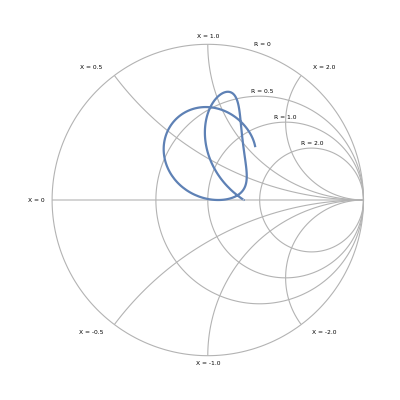

```mathematica
SmithPlot[{50+30ⅈ+30(Cos[ω^1.1]+ⅈ Sin[ω 1.1])},{ω,1,10}]
```

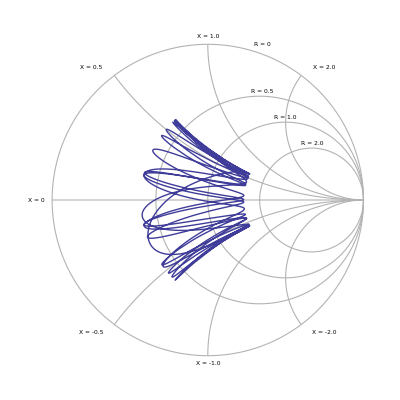

```mathematica
SmithPlot[{50+30(Cos[ω^2.1]+ⅈ Sin[ω 2.1])},{ω,1,10}]
```

## The circuit demonstration examples

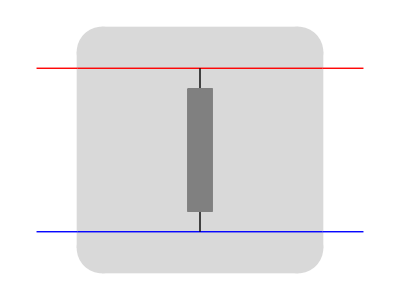

```mathematica
CircuitGraphics[TwoportShunt[OneportZ[z1]]]
```

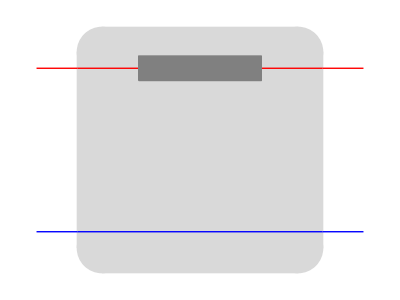

```mathematica
CircuitGraphics[TwoportSeries[OneportZ[z1]]]
```

```mathematica
TwoportShunt[OneportZ[z1]]CircuitGraphics[BasicCircuit]
```

### Basic usage example

We will construct a simple resonant circuit. We start by cascading two two-ports, a resistor onject in parallel with capacitor object as a series two-port, and a shunt inductor two-port. Note that we specify the primitives as objects, so that their impedances will be correctly computed. At this point all component values are symbols:

```mathematica
BasicCircuitParameters={c1->10. 10^-12,l1->.2 10^-6,r1->.1};BasicCircuit=CircuitCascade[TwoportSeries[OneportSeries[OneportC[c1],OneportR[r1]]] ,TwoportShunt[OneportL[l1]]]
```

CircuitCascade[TwoportSeries[OneportSeries[OneportC[c1],OneportR[r1]]],TwoportShunt[OneportL[l1]]]

We now check whether the circuit is arranged the way we intended by plotting it.

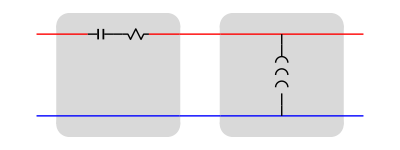

```mathematica
CircuitGraphics[BasicCircuit]
```

Our next step is to compute the ABCD matrix of the circuit. This is achieved by a simple conversion, for which we specify the frequency parameter.

```mathematica
BasicCircuitExpression=CircuitExpression[BasicCircuit,ω]//MatrixForm
```

(1-(ⅈ (r1-ⅈ/(c1 ω)))/(l1 ω) | r1-ⅈ/(c1 ω)
-ⅈ/(l1 ω) | 1)

We can obtain this object as a pretty printed matrix by using Mathematica’s built-in function:

```mathematica
MatrixForm[BasicCircuitExpression]
```

(1-(ⅈ (r1-ⅈ/(c1 ω)))/(l1 ω) | r1-ⅈ/(c1 ω)
-ⅈ/(l1 ω) | 1)

Next, we compute the circuit’s s-parameters. We have to choose input and output impedances. We use a very high impedance at the right end of the circuit, and a 50 Ω resistor for the cable.

```mathematica
BasicCircuitExpressionSparam=ToS[BasicCircuitExpression,{50.,1. 10^7}]//Chop
```

^S{{(1/50 (r1-ⅈ/(c1 ω))+(50 ⅈ)/(l1 ω)-(ⅈ (r1-ⅈ/(c1 ω)))/(l1 ω))/(2+1/50 (r1-ⅈ/(c1 ω))-(50 ⅈ)/(l1 ω)-(ⅈ (r1-ⅈ/(c1 ω)))/(l1 ω)),0.00447214/(2+1/50 (r1-ⅈ/(c1 ω))-(50 ⅈ)/(l1 ω)-(ⅈ (r1-ⅈ/(c1 ω)))/(l1 ω))},{894.427/(2+1/50 (r1-ⅈ/(c1 ω))-(50 ⅈ)/(l1 ω)-(ⅈ (r1-ⅈ/(c1 ω)))/(l1 ω)),(1/50 (r1-ⅈ/(c1 ω))+(50 ⅈ)/(l1 ω)+(ⅈ (r1-ⅈ/(c1 ω)))/(l1 ω))/(2+1/50 (r1-ⅈ/(c1 ω))-(50 ⅈ)/(l1 ω)-(ⅈ (r1-ⅈ/(c1 ω)))/(l1 ω))}}

We pick out s_11 and plot its amplitude over a range of frequencies. We also remember to inser numerical values for the circuit parameters. We  plot the argument of  s_11, which gives us the phase.

```mathematica
BasicCircuitExpressionSparam/.BasicCircuitParameters
```

^S{{(1/50 (0.1-(0.+1.×10^11 ⅈ)/ω)+(0.+2.5×10^8 ⅈ)/ω-((0.+5.×10^6 ⅈ) (0.1-(0.+1.×10^11 ⅈ)/ω))/ω)/(2+1/50 (0.1-(0.+1.×10^11 ⅈ)/ω)-(0.+2.5×10^8 ⅈ)/ω-((0.+5.×10^6 ⅈ) (0.1-(0.+1.×10^11 ⅈ)/ω))/ω),0.00447214/(2+1/50 (0.1-(0.+1.×10^11 ⅈ)/ω)-(0.+2.5×10^8 ⅈ)/ω-((0.+5.×10^6 ⅈ) (0.1-(0.+1.×10^11 ⅈ)/ω))/ω)},{894.427/(2+1/50 (0.1-(0.+1.×10^11 ⅈ)/ω)-(0.+2.5×10^8 ⅈ)/ω-((0.+5.×10^6 ⅈ) (0.1-(0.+1.×10^11 ⅈ)/ω))/ω),(1/50 (0.1-(0.+1.×10^11 ⅈ)/ω)+(0.+2.5×10^8 ⅈ)/ω+((0.+5.×10^6 ⅈ) (0.1-(0.+1.×10^11 ⅈ)/ω))/ω)/(2+1/50 (0.1-(0.+1.×10^11 ⅈ)/ω)-(0.+2.5×10^8 ⅈ)/ω-((0.+5.×10^6 ⅈ) (0.1-(0.+1.×10^11 ⅈ)/ω))/ω)}}

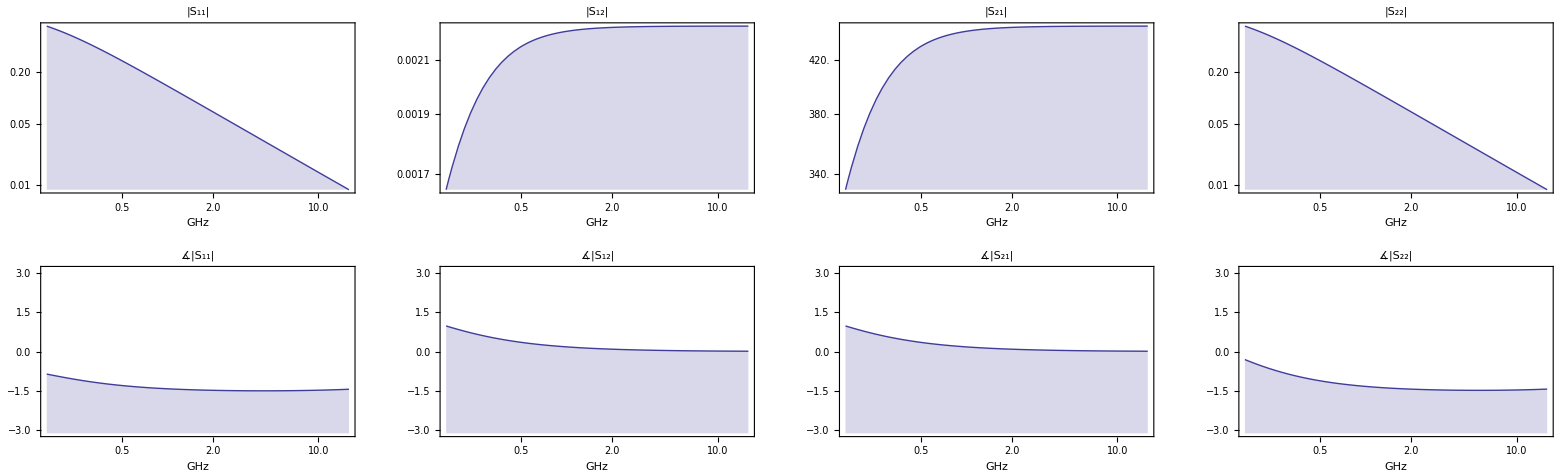

```mathematica
LogLinearPlotSparameters[BasicCircuitExpressionSparam/.BasicCircuitParameters,{ω, 10^9, 10^11}]
```

```mathematica
List@@(BasicCircuitExpressionSparam/.BasicCircuitParameters)
```

{{(1/50 (0.1-(0.+1.×10^11 ⅈ)/ω)+(0.+2.5×10^8 ⅈ)/ω-((0.+5.×10^6 ⅈ) (0.1-(0.+1.×10^11 ⅈ)/ω))/ω)/(2+1/50 (0.1-(0.+1.×10^11 ⅈ)/ω)-(0.+2.5×10^8 ⅈ)/ω-((0.+5.×10^6 ⅈ) (0.1-(0.+1.×10^11 ⅈ)/ω))/ω),0.00447214/(2+1/50 (0.1-(0.+1.×10^11 ⅈ)/ω)-(0.+2.5×10^8 ⅈ)/ω-((0.+5.×10^6 ⅈ) (0.1-(0.+1.×10^11 ⅈ)/ω))/ω)},{894.427/(2+1/50 (0.1-(0.+1.×10^11 ⅈ)/ω)-(0.+2.5×10^8 ⅈ)/ω-((0.+5.×10^6 ⅈ) (0.1-(0.+1.×10^11 ⅈ)/ω))/ω),(1/50 (0.1-(0.+1.×10^11 ⅈ)/ω)+(0.+2.5×10^8 ⅈ)/ω+((0.+5.×10^6 ⅈ) (0.1-(0.+1.×10^11 ⅈ)/ω))/ω)/(2+1/50 (0.1-(0.+1.×10^11 ⅈ)/ω)-(0.+2.5×10^8 ⅈ)/ω-((0.+5.×10^6 ⅈ) (0.1-(0.+1.×10^11 ⅈ)/ω))/ω)}}

```mathematica
?BodePlot
```

BodePlot[lsys] generates a Bode plot of a linear time-invariant system lsys.
BodePlot[lsys,{ω_min,ω_max}] plots for the frequency range ω_min to ω_max.
BodePlot[expr,{ω,ω_min,ω_max}] plots expr using the variable ω.

```mathematica
wwwwwwwwwwwwww
```

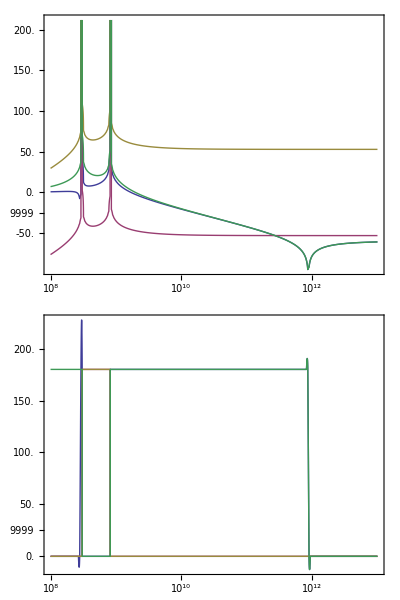

```mathematica
BodePlot[List@@(BasicCircuitExpressionSparam/.BasicCircuitParameters),{10^8,10^13}]
```

We can now plot these on a Smith chart.

```mathematica
(ToZ[BasicCircuitExpression]/.BasicCircuitParameters)[[1]]
```

{0.1-(0.+1.×10^11 ⅈ)/ω+(0.+2.×10^-7 ⅈ) ω,(0.-2.×10^-7 ⅈ) ω}

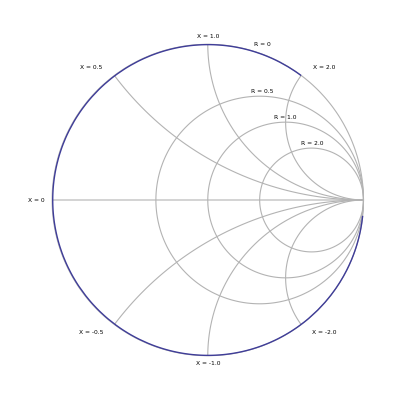
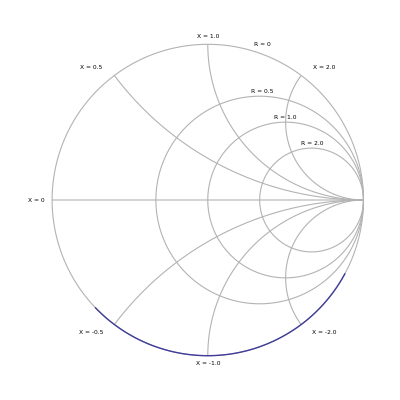

```mathematica
SmithPlot[#,{ω, 10^8, 10^9}]&/@(ToZ[BasicCircuitExpression]/.BasicCircuitParameters)[[1]]
```

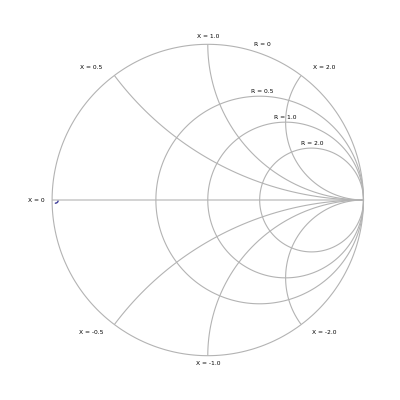
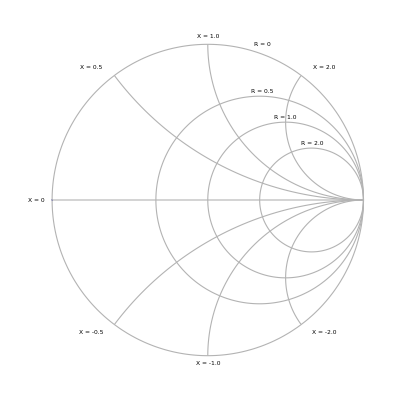

```mathematica
SmithPlot[#,{ω, 10^8, 10^9}]&/@(BasicCircuitExpressionSparam/.BasicCircuitParameters)[[1]]
```

We can also perform a parametric study, for example, we could investigate the effect of varying the value of the circuit elements. It is a good idea to initialise them first.

```mathematica
C1=10^-12;R1=1;L1=10^-7;
Panel[Column[{Row[{"cap: ",Slider[Dynamic[C1],{10^-12,20. 10^-12}],Dynamic[C1]}],Row[{"res: ",Slider[Dynamic[R1],{0,10}],Dynamic[R1]}],Row[{"lin: ",Slider[Dynamic[L1],{10^-7,1 10^-6}],Dynamic[L1]}],Dynamic[PlotSparameters[BasicCircuitExpressionSparam/.{c1->C1,l1->L1,r1->R1},{ω, 10^8, 10^10}]]}]]
```

cap: 
res: 
lin:

```mathematica
{Im[Dot[ToZ[(BasicCircuitExpressionSparam/.BasicCircuitParameters)],{Sin[ω t],Cos[ω t]}][[1]]],10Sin[ω t],ω t}/.ω-> 10 10^9
```

{Im[(-1.60982×10^-14-4.47214 ⅈ) Cos[10000000000 t]+(0.1+1990. ⅈ) Sin[10000000000 t]],10 Sin[10000000000 t],10000000000 t}

### Highpass

CircuitCascade[TwoportSeries[OneportC[c1]],TwoportShunt[OneportL[l1]]]

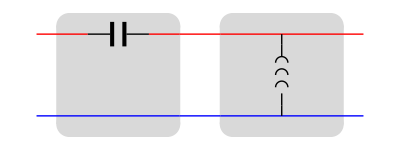

^A{{1-1/(c1 l1 ω^2),-ⅈ/(c1 ω)},{-ⅈ/(l1 ω),1}}

(1-1/(c1 l1 ω^2) | -ⅈ/(c1 ω)
-ⅈ/(l1 ω) | 1)

^S{{(-1/(c1 l1 ω^2)-ⅈ/(50 c1 ω)+(50 ⅈ)/(l1 ω))/(2-1/(c1 l1 ω^2)-ⅈ/(50 c1 ω)-(50 ⅈ)/(l1 ω)),0.00447214/(2-1/(c1 l1 ω^2)-ⅈ/(50 c1 ω)-(50 ⅈ)/(l1 ω))},{894.427/(2-1/(c1 l1 ω^2)-ⅈ/(50 c1 ω)-(50 ⅈ)/(l1 ω)),(1/(c1 l1 ω^2)-ⅈ/(50 c1 ω)+(50 ⅈ)/(l1 ω))/(2-1/(c1 l1 ω^2)-ⅈ/(50 c1 ω)-(50 ⅈ)/(l1 ω))}}

```mathematica
HighpassCircuit=CircuitCascade[TwoportSeries[OneportC[c1]] ,TwoportShunt[OneportL[l1]]]
CircuitGraphics[HighpassCircuit]
HighpassCircuitExpression=CircuitExpression[HighpassCircuit,ω]
MatrixForm[HighpassCircuitExpression]
HighpassCircuitExpressionSparam=ToS[HighpassCircuitExpression,{50.,1. 10^7}]//Chop
HighpassCircuitParameters={c1->10. 10^-10,l1->.2 10^-6};
```

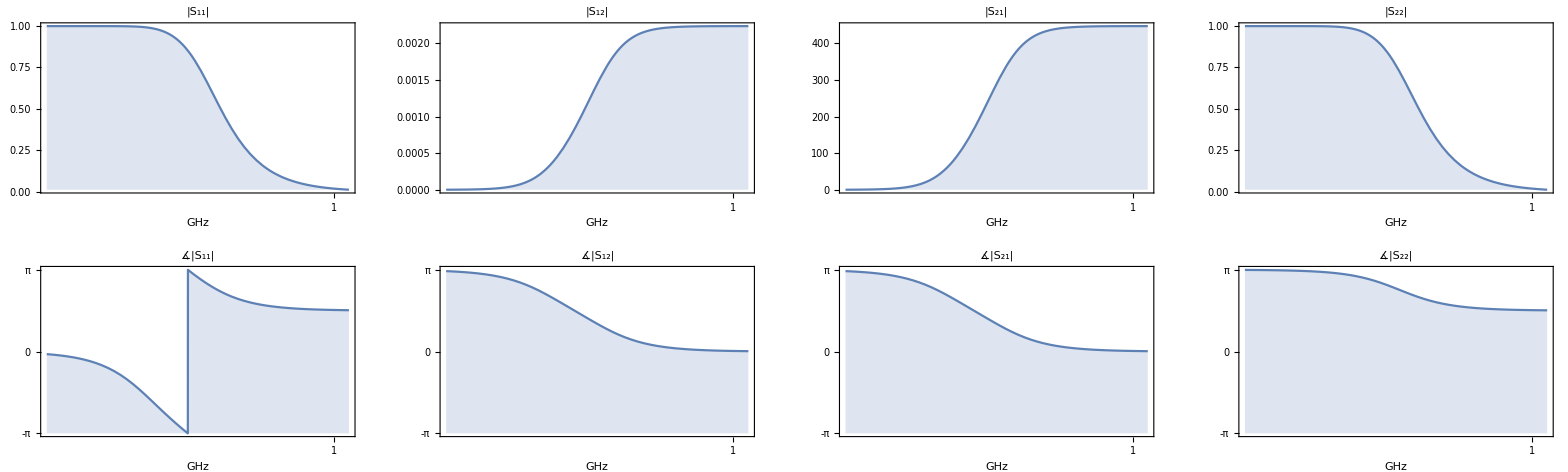

```mathematica
LogLinearPlotSparameters[HighpassCircuitExpressionSparam/.HighpassCircuitParameters,{ω,1 10^6, 10^10}]
```

### Lowpass

CircuitCascade[TwoportSeries[OneportL[l1]],TwoportShunt[OneportC[c1]]]

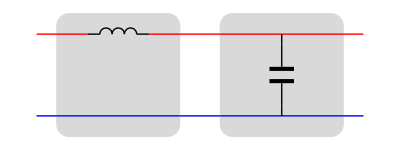

^A{{1-c1 l1 ω^2,ⅈ l1 ω},{ⅈ c1 ω,1}}

(1-c1 l1 ω^2 | ⅈ l1 ω
ⅈ c1 ω | 1)

^S{{(-50 ⅈ c1 ω+(ⅈ l1 ω)/50-c1 l1 ω^2)/(2+50 ⅈ c1 ω+(ⅈ l1 ω)/50-c1 l1 ω^2),0.00447214/(2+50 ⅈ c1 ω+(ⅈ l1 ω)/50-c1 l1 ω^2)},{894.427/(2+50 ⅈ c1 ω+(ⅈ l1 ω)/50-c1 l1 ω^2),(-50 ⅈ c1 ω+(ⅈ l1 ω)/50+c1 l1 ω^2)/(2+50 ⅈ c1 ω+(ⅈ l1 ω)/50-c1 l1 ω^2)}}

```mathematica
LowpassCircuit=CircuitCascade[TwoportSeries[OneportL[l1]] ,TwoportShunt[OneportC[c1]]]
CircuitGraphics[LowpassCircuit]
LowpassCircuitExpression=CircuitExpression[LowpassCircuit,ω]
MatrixForm[LowpassCircuitExpression]
LowpassCircuitExpressionSparam=ToS[LowpassCircuitExpression,{50.,1. 10^7}]//Chop
LowpassCircuitParameters={c1->10. 10^-10,l1->.2 10^-6};
```

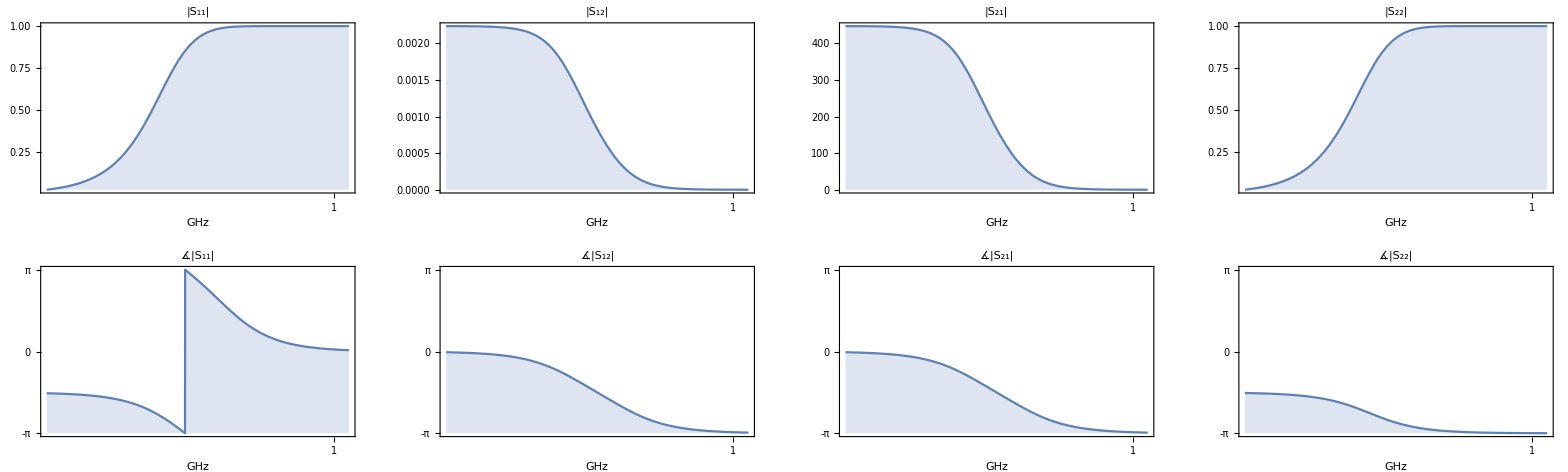

```mathematica
LogLinearPlotSparameters[LowpassCircuitExpressionSparam/.LowpassCircuitParameters,{ω,1 10^6, 10^10}]
```

### Bandpass

CircuitCascade[CircuitCascade[TwoportSeries[OneportL[l1]],TwoportSeries[OneportC[c1]]],CircuitCascade[TwoportShunt[OneportC[c1]],TwoportShunt[OneportL[l1]]]]

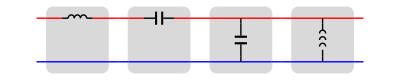

^A{{1+(-ⅈ/(l1 ω)+ⅈ c1 ω) (-ⅈ/(c1 ω)+ⅈ l1 ω),-ⅈ/(c1 ω)+ⅈ l1 ω},{-ⅈ/(l1 ω)+ⅈ c1 ω,1}}

^S{{(-50 (-ⅈ/(l1 ω)+ⅈ c1 ω)+1/50 (-ⅈ/(c1 ω)+ⅈ l1 ω)+(-ⅈ/(l1 ω)+ⅈ c1 ω) (-ⅈ/(c1 ω)+ⅈ l1 ω))/(2+50 (-ⅈ/(l1 ω)+ⅈ c1 ω)+1/50 (-ⅈ/(c1 ω)+ⅈ l1 ω)+(-ⅈ/(l1 ω)+ⅈ c1 ω) (-ⅈ/(c1 ω)+ⅈ l1 ω)),0.00447214/(2+50 (-ⅈ/(l1 ω)+ⅈ c1 ω)+1/50 (-ⅈ/(c1 ω)+ⅈ l1 ω)+(-ⅈ/(l1 ω)+ⅈ c1 ω) (-ⅈ/(c1 ω)+ⅈ l1 ω))},{894.427/(2+50 (-ⅈ/(l1 ω)+ⅈ c1 ω)+1/50 (-ⅈ/(c1 ω)+ⅈ l1 ω)+(-ⅈ/(l1 ω)+ⅈ c1 ω) (-ⅈ/(c1 ω)+ⅈ l1 ω)),(-50 (-ⅈ/(l1 ω)+ⅈ c1 ω)+1/50 (-ⅈ/(c1 ω)+ⅈ l1 ω)-(-ⅈ/(l1 ω)+ⅈ c1 ω) (-ⅈ/(c1 ω)+ⅈ l1 ω))/(2+50 (-ⅈ/(l1 ω)+ⅈ c1 ω)+1/50 (-ⅈ/(c1 ω)+ⅈ l1 ω)+(-ⅈ/(l1 ω)+ⅈ c1 ω) (-ⅈ/(c1 ω)+ⅈ l1 ω))}}

```mathematica
BandpassCircuit=CircuitCascade[CircuitCascade[TwoportSeries[OneportL[l1]] ,TwoportSeries[OneportC[c1]]] ,CircuitCascade[TwoportShunt[OneportC[c1]],TwoportShunt[OneportL[l1]] ]]
CircuitGraphics[BandpassCircuit]
BandpassCircuitExpression=CircuitExpression[BandpassCircuit,ω]
BandpassCircuitExpressionSparam=ToS[BandpassCircuitExpression,{50.,1. 10^7}]//Chop
BandpassCircuitParameters={c1->10. 10^-10,l1->.2 10^-6};
```

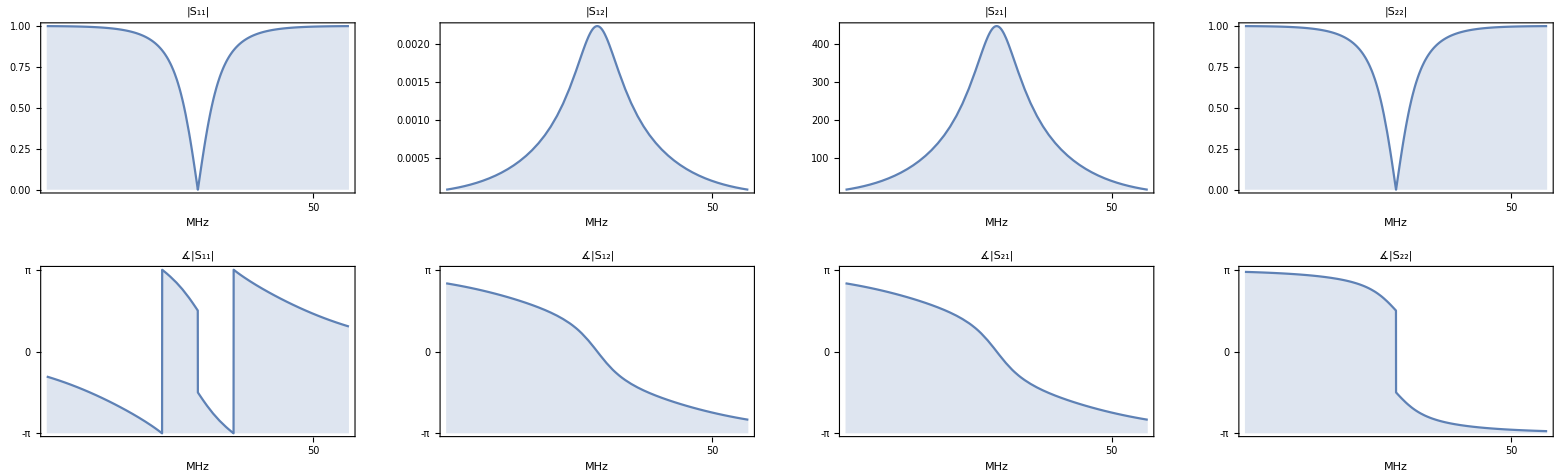

```mathematica
LogLinearPlotSparameters[BandpassCircuitExpressionSparam/.BandpassCircuitParameters,{ω, 10^7,5 10^8}]
```

### 5 Pole lowpass elliptic

From Bahl, chapter 12

CircuitCascade[TwoportSeries[OneportL[l1]],CircuitCascade[TwoportPi[OneportSeries[OneportL[l2],OneportC[c2]],OneportL[l3],OneportSeries[OneportL[l4],OneportC[c4]]],TwoportSeries[OneportL[l5]]]]

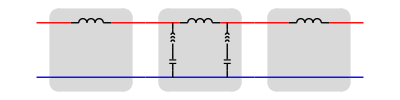

```mathematica
fivePoleLowpassCircuitParameters={c2->23 10^-12,c4->19.5 10^-12,l1->45.7 10^-9,l2->7.7 10^-9,l3->79.2 10^-9,l4->23 10^-9,l5->34.7 10^-9};
thePie=TwoportPi[OneportSeries[OneportL[l2],OneportC[c2]],OneportL[l3],OneportSeries[OneportL[l4],OneportC[c4]]];
fivePoleLowpassCircuit=CircuitCascade[TwoportSeries[OneportL[l1]],CircuitCascade[TwoportPi[OneportSeries[OneportL[l2],OneportC[c2]],OneportL[l3],OneportSeries[OneportL[l4],OneportC[c4]]],TwoportSeries[OneportL[l5]]]]
CircuitGraphics[fivePoleLowpassCircuit]
```

```mathematica
fivePoleLowpassCircuitExpression=CircuitExpression[fivePoleLowpassCircuit/.fivePoleLowpassCircuitParameters,ω]//Simplify
```

^A{{(0.+0. ⅈ)+((-2.22965×10^18+0. ⅈ)+(4.44348+0. ⅈ) ω^2)/((-2.22965×10^18+0. ⅈ)+ω^2)+((-2.44525×10^19+0. ⅈ) ω^2+(28.3593+0. ⅈ) ω^4)/((1.25898×10^37+0. ⅈ)-(7.87618×10^18+0. ⅈ) ω^2+(1.+0. ⅈ) ω^4),((0.+2.52971×10^67 ⅈ) ω-(0.+6.40235×10^49 ⅈ) ω^3+(0.+5.39826×10^31 ⅈ) ω^5-(0.+1.74794×10^13 ⅈ) ω^7+(0.+1.73321×10^-6 ⅈ) ω^9)/((1.58503×10^74+0. ⅈ)-(1.98319×10^56+0. ⅈ) ω^2+(8.72138×10^37+0. ⅈ) ω^4-(1.57524×10^19+0. ⅈ) ω^6+(1.+0. ⅈ) ω^8)},{((0.+5.35067×10^26 ⅈ) ω-(0.+6.20553×10^8 ⅈ) ω^3)/((1.25898×10^37+0. ⅈ)-(7.87618×10^18+0. ⅈ) ω^2+(1.+0. ⅈ) ω^4),((7.10887×10^55+0. ⅈ)-(2.91396×10^38+0. ⅈ) ω^2+(2.34689×10^20+0. ⅈ) ω^4-(32.8189+0. ⅈ) ω^6)/((7.10887×10^55+0. ⅈ)-(5.70629×10^37+0. ⅈ) ω^2+(1.35227×10^19+0. ⅈ) ω^4-(1.+0. ⅈ) ω^6)}}

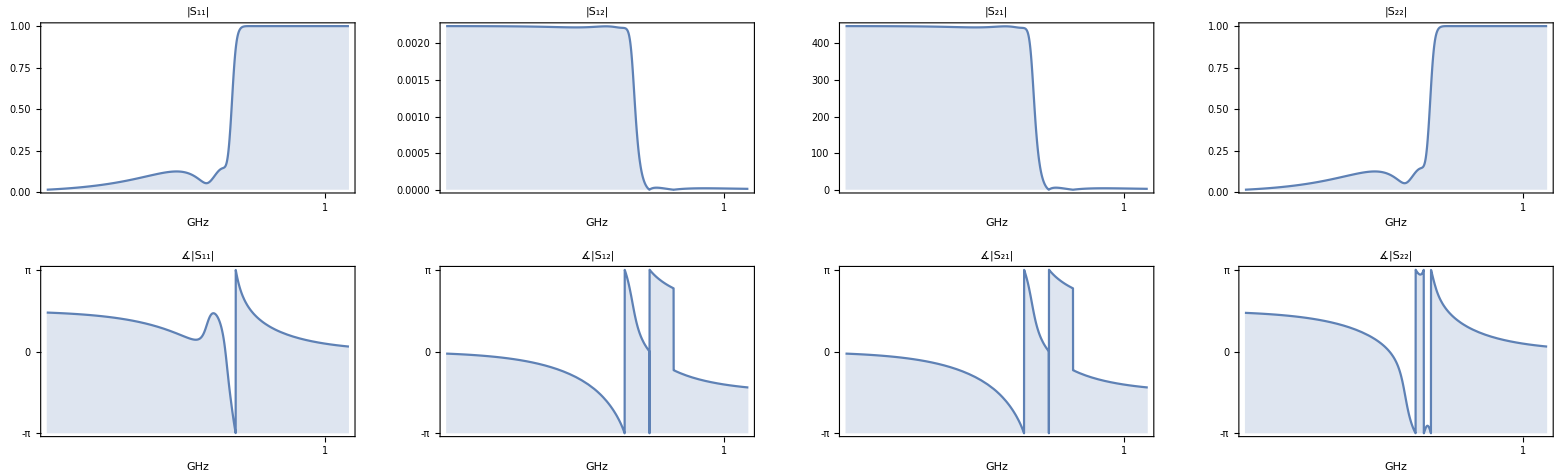

```mathematica
fivePoleLowpassCircuitExpressionSparam=ToS[fivePoleLowpassCircuitExpression,{50.,1. 10^7}];
LogLinearPlotSparameters[fivePoleLowpassCircuitExpressionSparam,{ω,3 10^7,10 10^9}]
```

### 3 Pole bandpass

From Bahl, chapter 12

CircuitCascade[TwoportPi[OneportC[c1],OneportC[c2],OneportC[c3]],CircuitCascade[TwoportSeries[OneportParallel[OneportC[c4],OneportL[l1]]],CircuitCascade[TwoportPi[OneportC[c4],OneportC[c5],OneportC[c4]],CircuitCascade[TwoportSeries[OneportParallel[OneportC[c4],OneportL[l1]]],CircuitCascade[TwoportPi[OneportC[c4],OneportC[c5],OneportC[c4]],CircuitCascade[TwoportSeries[OneportParallel[OneportC[c4],OneportL[l1]]],TwoportPi[OneportC[c1],OneportC[c2],OneportC[c3]]]]]]]]

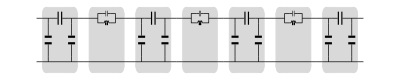

```mathematica
ThreepoleBandpassCircuitParameters={c1->0.1 10^-12,c2->.15481 10^-12,c3->.12258 10^-12,c4->.26309 10^-12,c5->.012438 10^-12,l1->10 10^-9};

firstPie=TwoportPi[OneportC[c1],OneportC[c2],OneportC[c3]];
secondPie=TwoportPi[OneportC[c4],OneportC[c5],OneportC[c4]];
serial=TwoportSeries[OneportParallel[OneportC[c4],OneportL[l1]]];

ThreepoleBandpassCircuit=CircuitCascade[firstPie,CircuitCascade[serial,CircuitCascade[secondPie,CircuitCascade[serial,CircuitCascade[secondPie,CircuitCascade[serial,firstPie]]]]]]

CircuitGraphics[ThreepoleBandpassCircuit]
```

```mathematica
ThreepoleBandpassCircuitExpression=CircuitExpression[ThreepoleBandpassCircuit/.ThreepoleBandpassCircuitParameters,ω]
```

^A{{-1/ω(0.+6.45953×10^12 ⅈ) ((0.+0. ⅈ)+(0.+3.89849×10^-10 ⅈ) ω+((4.07168×10^-23+0. ⅈ) ω^3)/((0.+1.×10^8 ⅈ)-(0.+2.6309×10^-13 ⅈ) ω^2)+((0.-3.89547×10^6 ⅈ) ω+(0.+3.52884×10^-14 ⅈ) ω^3-(0.+7.7073×10^-35 ⅈ) ω^5)/((0.+1.×10^8 ⅈ)-(0.+2.6309×10^-13 ⅈ) ω^2)^2)+(1.79181+0. ⅈ) (((-2.83162×10^19+0. ⅈ)+(0.217565+0. ⅈ) ω^2-(4.17113×10^-22+0. ⅈ) ω^4)/((0.+1.×10^8 ⅈ)-(0.+2.6309×10^-13 ⅈ) ω^2)^2+(ω ((0.+0. ⅈ)+(0.+3.89849×10^-10 ⅈ) ω+((4.07168×10^-23+0. ⅈ) ω^3)/((0.+1.×10^8 ⅈ)-(0.+2.6309×10^-13 ⅈ) ω^2)+((0.-3.89547×10^6 ⅈ) ω+(0.+3.52884×10^-14 ⅈ) ω^3-(0.+7.7073×10^-35 ⅈ) ω^5)/((0.+1.×10^8 ⅈ)-(0.+2.6309×10^-13 ⅈ) ω^2)^2))/((0.-1.×10^8 ⅈ)+(0.+2.6309×10^-13 ⅈ) ω^2)),-((0.+6.45953×10^12 ⅈ) ((3.35692×10^35+0. ⅈ)-(4.43862×10^15+0. ⅈ) ω^2+(0.0000217021+0. ⅈ) ω^4-(4.64767×10^-26+0. ⅈ) ω^6+(3.68065×10^-47+0. ⅈ) ω^8))/(ω ((1.×10^32+0. ⅈ)-(1.05236×10^12+0. ⅈ) ω^2+(4.15298×10^-9+0. ⅈ) ω^4-(7.28405×10^-30+0. ⅈ) ω^6+(4.7909×10^-51+0. ⅈ) ω^8))+((0.+2.48405×10^129 ⅈ) (1.2196×10^88-3.55278×10^68 ω^2+4.55142×10^48 ω^4-3.36821×10^28 ω^6+1.58796×10^8 ω^8-4.94941×10^-13 ω^10+1.02049×10^-33 ω^12-1.34296×10^-54 ω^14+1.02409×10^-75 ω^16-3.44944×10^-97 ω^18))/(ω (-1.38633×10^201+3.28258×10^181 ω^2-3.45445×10^161 ω^4+2.12061×10^141 ω^6-8.36866×10^120 ω^8+2.20171×10^100 ω^10-3.86166×10^79 ω^12+4.35413×10^58 ω^14-2.86382×10^37 ω^16+8.37158×10^15 ω^18))},{(1.64595+0. ⅈ) ((0.+0. ⅈ)+(0.+3.89849×10^-10 ⅈ) ω+((4.07168×10^-23+0. ⅈ) ω^3)/((0.+1.×10^8 ⅈ)-(0.+2.6309×10^-13 ⅈ) ω^2)+((0.-3.89547×10^6 ⅈ) ω+(0.+3.52884×10^-14 ⅈ) ω^3-(0.+7.7073×10^-35 ⅈ) ω^5)/((0.+1.×10^8 ⅈ)-(0.+2.6309×10^-13 ⅈ) ω^2)^2)+(0.+3.01761×10^-13 ⅈ) ω (((-2.83162×10^19+0. ⅈ)+(0.217565+0. ⅈ) ω^2-(4.17113×10^-22+0. ⅈ) ω^4)/((0.+1.×10^8 ⅈ)-(0.+2.6309×10^-13 ⅈ) ω^2)^2+(ω ((0.+0. ⅈ)+(0.+3.89849×10^-10 ⅈ) ω+((4.07168×10^-23+0. ⅈ) ω^3)/((0.+1.×10^8 ⅈ)-(0.+2.6309×10^-13 ⅈ) ω^2)+((0.-3.89547×10^6 ⅈ) ω+(0.+3.52884×10^-14 ⅈ) ω^3-(0.+7.7073×10^-35 ⅈ) ω^5)/((0.+1.×10^8 ⅈ)-(0.+2.6309×10^-13 ⅈ) ω^2)^2))/((0.-1.×10^8 ⅈ)+(0.+2.6309×10^-13 ⅈ) ω^2)),((1.64595+0. ⅈ) ((3.35692×10^35+0. ⅈ)-(4.43862×10^15+0. ⅈ) ω^2+(0.0000217021+0. ⅈ) ω^4-(4.64767×10^-26+0. ⅈ) ω^6+(3.68065×10^-47+0. ⅈ) ω^8))/((1.×10^32+0. ⅈ)-(1.05236×10^12+0. ⅈ) ω^2+(4.15298×10^-9+0. ⅈ) ω^4-(7.28405×10^-30+0. ⅈ) ω^6+(4.7909×10^-51+0. ⅈ) ω^8)-((4.18342×10^116+0. ⅈ) (1.2196×10^88-3.55278×10^68 ω^2+4.55142×10^48 ω^4-3.36821×10^28 ω^6+1.58796×10^8 ω^8-4.94941×10^-13 ω^10+1.02049×10^-33 ω^12-1.34296×10^-54 ω^14+1.02409×10^-75 ω^16-3.44944×10^-97 ω^18))/(-1.38633×10^201+3.28258×10^181 ω^2-3.45445×10^161 ω^4+2.12061×10^141 ω^6-8.36866×10^120 ω^8+2.20171×10^100 ω^10-3.86166×10^79 ω^12+4.35413×10^58 ω^14-2.86382×10^37 ω^16+8.37158×10^15 ω^18)}}

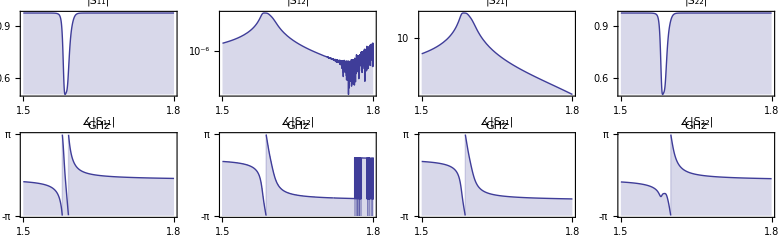

```mathematica
ThreepoleBandpassCircuitExpressionSparam=ToS[ThreepoleBandpassCircuitExpression,{50.,1. 10^7}];
LogLinearPlotSparameters[ThreepoleBandpassCircuitExpressionSparam,{ω,1.5 10^10,1.8 10^10}]
```

### 90° Hybrid (NOT DONE)

From Bahl, chapter 12

First we analyse an arm of the hybrid. It is either a waveguide, or a lumped π network. Let us see the relation:

```mathematica
w=CircuitExpression[TwoportWaveguide[z0,θ/l,l],ω]
```

^A{{Cos[θ],ⅈ z0 Sin[θ]},{(ⅈ Sin[θ])/z0,Cos[θ]}}

```mathematica
p=CircuitExpression[TwoportPi[OneportC[c1],OneportL[l1],OneportC[c1]],ω]//FullSimplify
```

^A{{1-c1 l1 ω^2,ⅈ l1 ω},{-ⅈ c1 ω (-2+c1 l1 ω^2),1-c1 l1 ω^2}}

```mathematica
MapThread[Equal,{Flatten[List@@w],Flatten[List@@p]}]
```

{Cos[θ]==1-c1 l1 ω^2,ⅈ z0 Sin[θ]==ⅈ l1 ω,(ⅈ Sin[θ])/z0==-ⅈ c1 ω (-2+c1 l1 ω^2),Cos[θ]==1-c1 l1 ω^2}

```mathematica
Solve[MapThread[Equal,{Flatten[List@@w],Flatten[List@@p]}],{θ,z0,l1}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{z0→(√(1-Cos[θ]^2))/(c1 ω+c1 ω Cos[θ]),l1→(1-Cos[θ]^2)/(ω (c1 ω+c1 ω Cos[θ]))},{z0→(√(1-Cos[θ]^2))/(-c1 ω-c1 ω Cos[θ]),l1→(1-Cos[θ]^2)/(c1 ω^2+c1 ω^2 Cos[θ])}}

### Directional coupler (NOT DONE)

### Waveguide vs Network (NOT DONE)

```mathematica
param={z0->50.,θ->20.};
CircuitExpression[TwoportWaveguide[z0,θ/l,l],ω]
CircuitExpression[TwoportPi[OneportC[1/z0 √((1-Cos[θ])/(1+Cos[θ]))],OneportL[(z0 Sin[θ])/ω],OneportC[1/z0 √((1-Cos[θ])/(1+Cos[θ]))]],ω]
```

^A{{Cos[θ],ⅈ z0 Sin[θ]},{(ⅈ Sin[θ])/z0,Cos[θ]}}

^A{{1-ω √((1-Cos[θ])/(1+Cos[θ])) Sin[θ],ⅈ z0 Sin[θ]},{(ⅈ ω √((1-Cos[θ])/(1+Cos[θ])))/z0+(ⅈ ω √((1-Cos[θ])/(1+Cos[θ])) (1-ω √((1-Cos[θ])/(1+Cos[θ])) Sin[θ]))/z0,1-ω √((1-Cos[θ])/(1+Cos[θ])) Sin[θ]}}

### A cable trap (NOT DONE)

```mathematica
cableCircuit=TwoportXsection[OneportC[c1],OneportL[l1]]
```

TwoportXsection[OneportC[c1],OneportL[l1]]

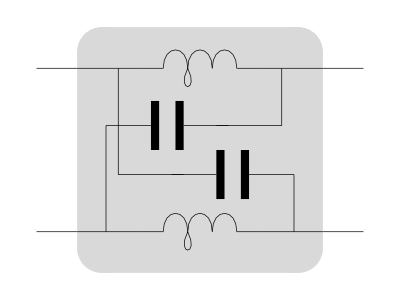

```mathematica
CircuitGraphics[cableCircuit]
```

```mathematica
cableCircuitExpression=CircuitExpression[cableCircuit,ω]/.{l1->10^(-9),c1->10^(-12)}
```

^A{{(-(1000000000000 ⅈ)/ω+(ⅈ ω)/1000000000)/(-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000),2000/(-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000)},{2/(-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000),(-(1000000000000 ⅈ)/ω+(ⅈ ω)/1000000000)/(-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000)}}

```mathematica
cableCircuitExpressionSparam=ToS[cableCircuitExpression,{50.,50}]//Chop
```

^S{{-(60/((140/(-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000)+(2 (-(1000000000000 ⅈ)/ω+(ⅈ ω)/1000000000))/(-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000)) (-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000))),(2. (-4000/(-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000)^2+(-(1000000000000 ⅈ)/ω+(ⅈ ω)/1000000000)^2/(-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000)^2))/(140/(-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000)+(2 (-(1000000000000 ⅈ)/ω+(ⅈ ω)/1000000000))/(-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000))},{2./(140/(-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000)+(2 (-(1000000000000 ⅈ)/ω+(ⅈ ω)/1000000000))/(-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000)),-(60/((140/(-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000)+(2 (-(1000000000000 ⅈ)/ω+(ⅈ ω)/1000000000))/(-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000)) (-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000)))}}

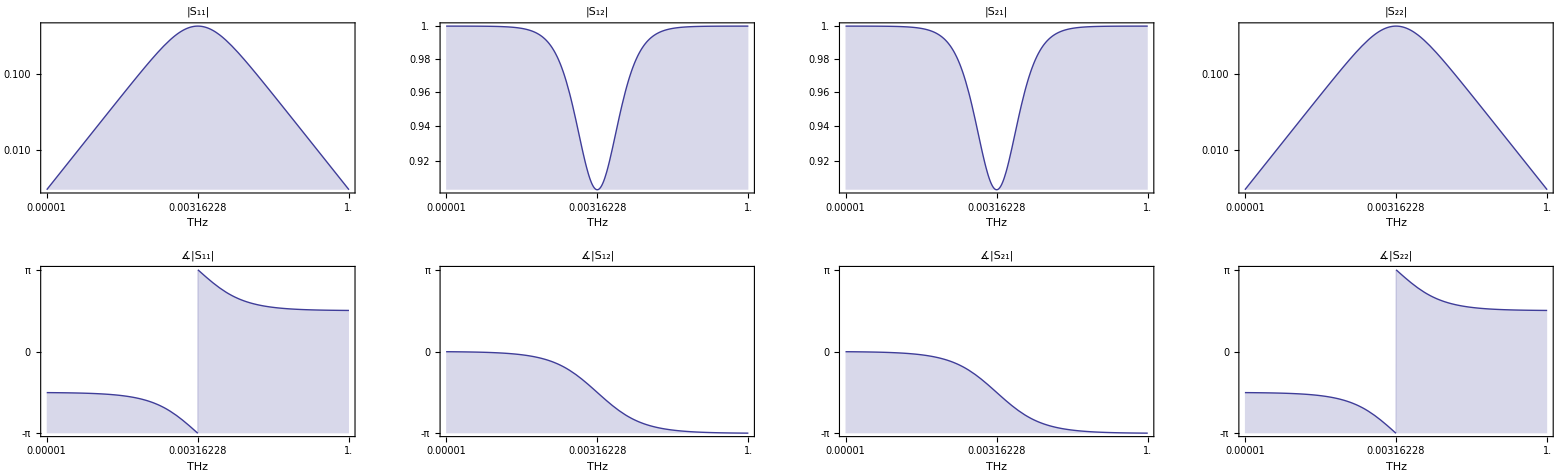

```mathematica
omin=10^8;omax=1 10^13;


LogLinearPlotSparameters[cableCircuitExpressionSparam,{ω,omin,omax}]
```

### A bridge circuit

```mathematica
bridgeCircuit=CircuitCascade[TwoportBridge[OneportR[r1],OneportR[r2],OneportR[r3],OneportR[r4]],TwoportShunt[OneportParallel[OneportL[l1],OneportC[c1]]]]
```

CircuitCascade[TwoportBridge[OneportR[r1],OneportR[r2],OneportR[r3],OneportR[r4]],TwoportShunt[OneportParallel[OneportL[l1],OneportC[c1]]]]

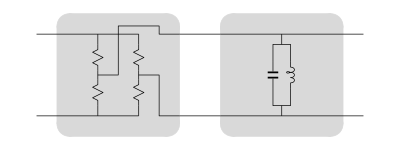

```mathematica
CircuitGraphics[bridgeCircuit]
```

```mathematica
bridgeCircuitExpression=CircuitExpression[bridgeCircuit,ω]/.{r1->10000,r2->20000,r3->10000,r4->40000,l1->10^(-9),c1->10^(-12)}
```

^A{{-15/2-110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000),-110000},{-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000),-6}}

```mathematica
bridgeCircuitExpressionSparam=ToS[bridgeCircuitExpression,{50.,1. 10^18}]//Chop
```

^S{{(-4403/2-50 (-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))-110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))/(-4427/2+50 (-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))-110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000)),(1.41421×10^-8 (-6 (-15/2-110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))+110000 (-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))))/(-4427/2+50 (-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))-110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))},{2.82843×10^8/(-4427/2+50 (-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))-110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000)),(-4397/2-50 (-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))+110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))/(-4427/2+50 (-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))-110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))}}

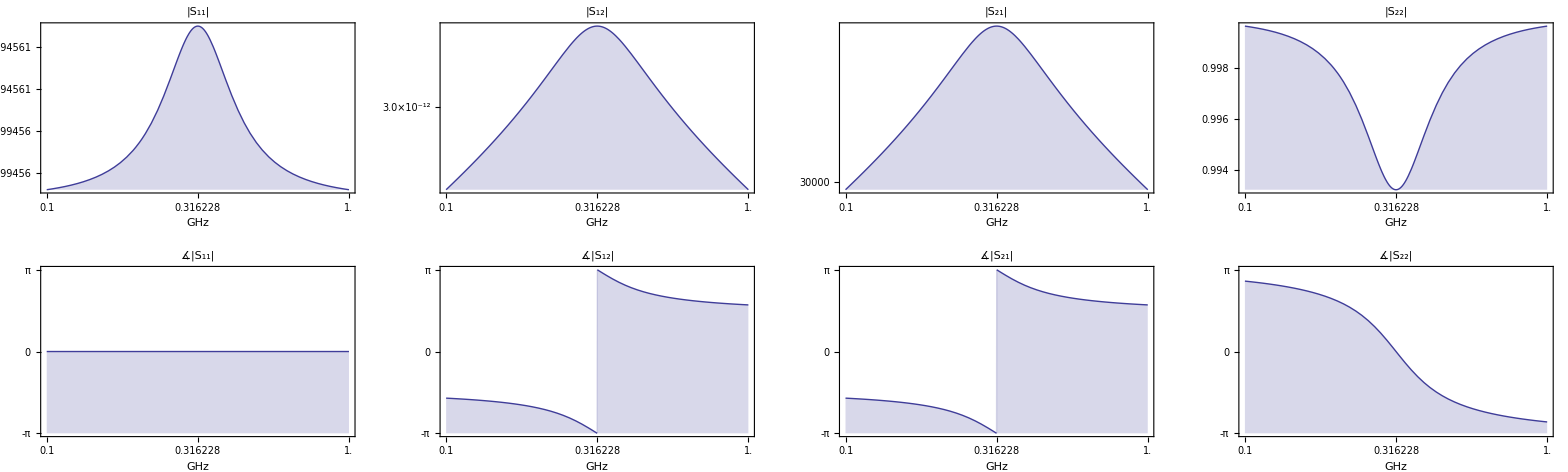

```mathematica
omin=10^10;omax=1 10^11;
LogLinearPlotSparameters[bridgeCircuitExpressionSparam,{ω,omin,omax}]
```

### MR sensor

CircuitCascade[TwoportShunt[OneportC[c1]],CircuitCascade[TwoportSeries[OneportC[c1]],TwoportShunt[OneportL[l1]]]]

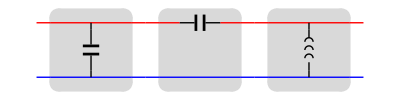

Export::nodir: Directory /Users/Jan G. Korvink/Desktop/DT/3 Temp Docs/CircuitTheory/ does not exist.

Export::noopen: Cannot open /Users/Jan G. Korvink/Desktop/DT/3 Temp Docs/CircuitTheory/mrcircuitpic.pdf.

$Failed

^A{{1-1/(c1 l1 ω^2),-ⅈ/(c1 ω)},{-ⅈ/(l1 ω)+ⅈ c1 (1-1/(c1 l1 ω^2)) ω,2}}

(1-1/(c1 l1 ω^2) | -ⅈ/(c1 ω)
-ⅈ/(l1 ω)+ⅈ c1 (1-1/(c1 l1 ω^2)) ω | 2)

^S{{(-1-1/(c1 l1 ω^2)-ⅈ/(50 c1 ω)-50 (-ⅈ/(l1 ω)+ⅈ c1 (1-1/(c1 l1 ω^2)) ω))/(3-1/(c1 l1 ω^2)-ⅈ/(50 c1 ω)+50 (-ⅈ/(l1 ω)+ⅈ c1 (1-1/(c1 l1 ω^2)) ω)),(0.00447214 (2 (1-1/(c1 l1 ω^2))+(ⅈ (-ⅈ/(l1 ω)+ⅈ c1 (1-1/(c1 l1 ω^2)) ω))/(c1 ω)))/(3-1/(c1 l1 ω^2)-ⅈ/(50 c1 ω)+50 (-ⅈ/(l1 ω)+ⅈ c1 (1-1/(c1 l1 ω^2)) ω))},{894.427/(3-1/(c1 l1 ω^2)-ⅈ/(50 c1 ω)+50 (-ⅈ/(l1 ω)+ⅈ c1 (1-1/(c1 l1 ω^2)) ω)),(1+1/(c1 l1 ω^2)-ⅈ/(50 c1 ω)-50 (-ⅈ/(l1 ω)+ⅈ c1 (1-1/(c1 l1 ω^2)) ω))/(3-1/(c1 l1 ω^2)-ⅈ/(50 c1 ω)+50 (-ⅈ/(l1 ω)+ⅈ c1 (1-1/(c1 l1 ω^2)) ω))}}

```mathematica
MRCircuit=CircuitCascade[TwoportShunt[OneportC[c1]] ,CircuitCascade[TwoportSeries[OneportC[c1]] ,TwoportShunt[OneportL[l1]]]]
mrcircuitpic=CircuitGraphics[MRCircuit]
Export["/Users/Jan G. Korvink/Desktop/DT/3 Temp Docs/CircuitTheory/mrcircuitpic.pdf",mrcircuitpic]
MRCircuitExpression=CircuitExpression[MRCircuit,ω]
MatrixForm[MRCircuitExpression]
MRCircuitExpressionSparam=ToS[MRCircuitExpression,{50.,1. 10^7}]//Chop
MRCircuitParameters={c1->10. 10^-10,l1->.2 10^-6};
```

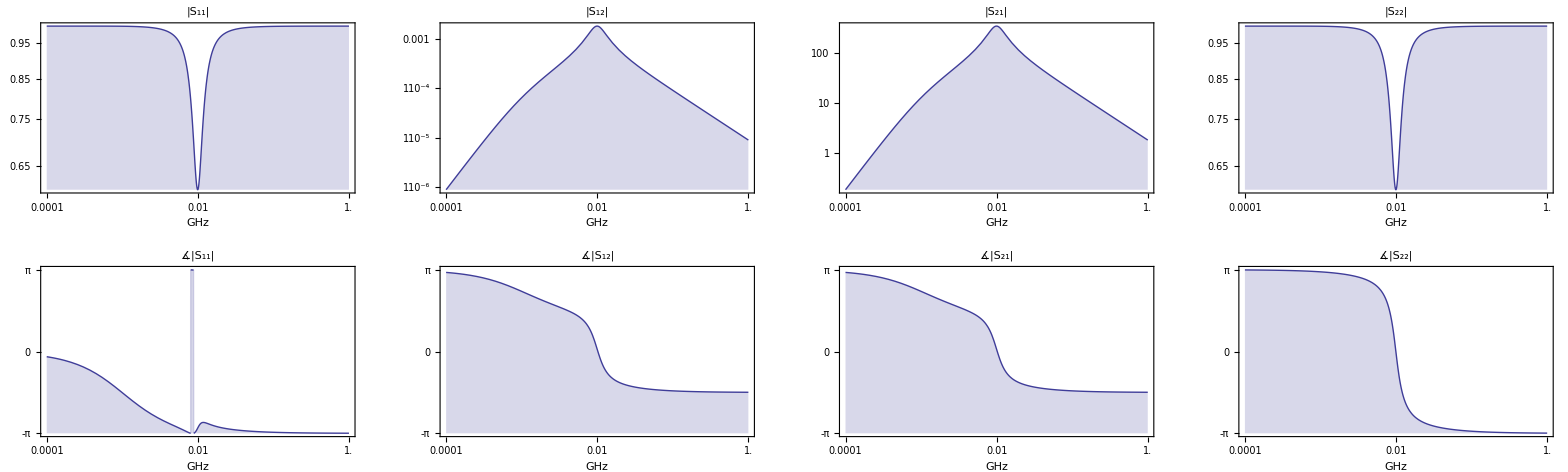

```mathematica
LogLinearPlotSparameters[MRCircuitExpressionSparam/.MRCircuitParameters,{ω,1 10^6, 10^10}]
```

### MR sensor with balanced output

CircuitCascade[TwoportBoxsection[OneportC[c1],OneportC[c2]],CircuitCascade[TwoportSeries[OneportC[c3]],TwoportShunt[OneportL[l1]]]]

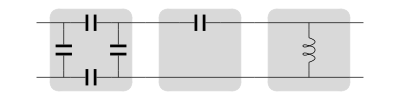

Export::nodir: Directory "/Users/Jan G. Korvink/Desktop/DT/3 Temp Docs/CircuitTheory/" does not exist.

Export::noopen: Cannot open "/Users/Jan G. Korvink/Desktop/DT/3 Temp Docs/CircuitTheory/mrcircuitpic.pdf".

$Failed

2 ^A{{((c1+c2) (1-1/(c3 l1 ω^2)))/c1-1/(c1 l1 ω^2),-ⅈ/(c1 ω)-(ⅈ (c1+c2))/(c1 c3 ω)},{-(ⅈ (c1+c2))/(c1 l1 ω)+(ⅈ c2 (2 c1+c2) (1-1/(c3 l1 ω^2)) ω)/c1,(c1+c2)/c1+(c2 (2 c1+c2))/(c1 c3)}}

2 ^A{{((c1+c2) (1-1/(c3 l1 ω^2)))/c1-1/(c1 l1 ω^2),-ⅈ/(c1 ω)-(ⅈ (c1+c2))/(c1 c3 ω)},{-(ⅈ (c1+c2))/(c1 l1 ω)+(ⅈ c2 (2 c1+c2) (1-1/(c3 l1 ω^2)) ω)/c1,(c1+c2)/c1+(c2 (2 c1+c2))/(c1 c3)}}

ToS[2 ^A{{((c1+c2) (1-1/(c3 l1 ω^2)))/c1-1/(c1 l1 ω^2),-ⅈ/(c1 ω)-(ⅈ (c1+c2))/(c1 c3 ω)},{-(ⅈ (c1+c2))/(c1 l1 ω)+(ⅈ c2 (2 c1+c2) (1-1/(c3 l1 ω^2)) ω)/c1,(c1+c2)/c1+(c2 (2 c1+c2))/(c1 c3)}},{50.,1.×10^7}]

```mathematica
MRCircuit=CircuitCascade[TwoportBoxsection[OneportC[c1],OneportC[c2]] ,CircuitCascade[TwoportSeries[OneportC[c3]],TwoportShunt[OneportL[l1]]]]
mrcircuitpic=CircuitGraphics[MRCircuit]
Export["/Users/Jan G. Korvink/Desktop/DT/3 Temp Docs/CircuitTheory/mrcircuitpic.pdf",mrcircuitpic]
MRCircuitExpression=CircuitExpression[MRCircuit,ω]
MatrixForm[MRCircuitExpression]
MRCircuitExpressionSparam=ToS[MRCircuitExpression,{50.,1. 10^7}]//Chop
MRCircuitParameters={c1->10. 10^-15,c2->10. 10^-15,c3->10. 10^-12,l1->.2 10^-6};
```

```mathematica
LogLinearPlotSparameters[MRCircuitExpressionSparam/.MRCircuitParameters,{ω,1 10^8, 10^10}]
```

LogLinearPlotSparameters[ToS[2 ^A{{2. (1-(5.×10^17)/ω^2)-(5.×10^20)/ω^2,-(0.+1.002×10^14 ⅈ)/ω},{-(0.+1.×10^7 ⅈ)/ω+(0.+3.×10^-14 ⅈ) (1-(5.×10^17)/ω^2) ω,2.003}},{50.,1.×10^7}],{ω,100000000,10000000000}]

```mathematica
CircuitExpression[TwoportBoxsection[OneportC[c1],OneportC[c2]],ω]
```

2 ^A{{(c1+c2)/c1,-ⅈ/(c1 ω)},{ⅈ c2 ω+(ⅈ c2 (c1+c2) ω)/c1,1+c2/c1}}

### Impedance spectroscopy (NOT DONE)

### Patrick Bollgrün’s flux guide

```mathematica
BasicCircuitParameters={c1->75. 10^-12,l1->80. 10^-9,m1->8. 10^-9,r1->.1};
```

```mathematica
baseCircuit=
CircuitCascade[TwoportSeries[OneportR[r1]],CircuitCascade[TwoportSeries[OneportC[c1]],CircuitCascade[TwoportSeries[OneportL[l1]] ,TwoportShunt[OneportL[m1]]]]]
```

CircuitCascade[TwoportSeries[OneportR[r1]],CircuitCascade[TwoportSeries[OneportC[c1]],CircuitCascade[TwoportSeries[OneportL[l1]],TwoportShunt[OneportL[m1]]]]]

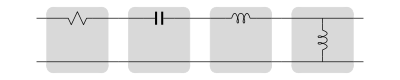

```mathematica
CircuitGraphics[baseCircuit,Frame->False]
```

```mathematica
doubleCircuit=CircuitCascade[baseCircuit,baseCircuit]
```

CircuitCascade[CircuitCascade[TwoportSeries[OneportR[r1]],CircuitCascade[TwoportSeries[OneportC[c1]],CircuitCascade[TwoportSeries[OneportL[l1]],TwoportShunt[OneportL[m1]]]]],CircuitCascade[TwoportSeries[OneportR[r1]],CircuitCascade[TwoportSeries[OneportC[c1]],CircuitCascade[TwoportSeries[OneportL[l1]],TwoportShunt[OneportL[m1]]]]]]

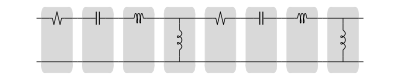

```mathematica
CircuitGraphics[doubleCircuit,Frame->False]
```

CircuitCascade[CircuitCascade[CircuitCascade[TwoportSeries[OneportR[r1]],CircuitCascade[TwoportSeries[OneportC[c1]],CircuitCascade[TwoportSeries[OneportL[l1]],TwoportShunt[OneportL[m1]]]]],CircuitCascade[TwoportSeries[OneportR[r1]],CircuitCascade[TwoportSeries[OneportC[c1]],CircuitCascade[TwoportSeries[OneportL[l1]],TwoportShunt[OneportL[m1]]]]]],CircuitCascade[CircuitCascade[TwoportSeries[OneportR[r1]],CircuitCascade[TwoportSeries[OneportC[c1]],CircuitCascade[TwoportSeries[OneportL[l1]],TwoportShunt[OneportL[m1]]]]],CircuitCascade[TwoportSeries[OneportR[r1]],CircuitCascade[TwoportSeries[OneportC[c1]],CircuitCascade[TwoportSeries[OneportL[l1]],TwoportShunt[OneportL[m1]]]]]]]

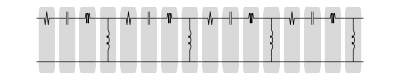

```mathematica
quadCircuit=CircuitCascade[doubleCircuit,doubleCircuit]
CircuitGraphics[quadCircuit,Frame->False]
```

```mathematica
baseCircuitExpression=CircuitExpression[baseCircuit,(2π) f]/.BasicCircuitParameters;
```

```mathematica
doubleCircuitExpression=CircuitExpression[doubleCircuit,(2π) f]/.BasicCircuitParameters;
```

```mathematica
quadCircuitExpression=CircuitExpression[quadCircuit,(2π)f]/.BasicCircuitParameters;
```

```mathematica
baseCircuitExpressionSparam=ToS[baseCircuitExpression,{50.,1. 10^9}];
```

```mathematica
doubleCircuitExpressionSparam=ToS[doubleCircuitExpression,{50.,1. 10^9}];
```

```mathematica
quadCircuitExpression
```

^A{{-1/f^6(0.+7.52432×10^49 ⅈ) (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)^2+1/f^8 3.17655×10^66 (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2)^2,1/f^5 3.78213×10^42 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)+1/f^7 1.59671×10^59 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2)},{-1/f^5(0.+3.54575×10^40 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)-1/f^7(0.+1.49692×10^57 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2),1/f^4 1.78229×10^33 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2-1/f^6(0.+7.52432×10^49 ⅈ) (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)^2}}

```mathematica
quadCircuitExpressionSparam=ToS[quadCircuitExpression,{50.,1. 10^9}]
```

^S{{((0.+0. ⅈ)-1/f^4 1.78229×10^33 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2+1/f^83.17655×10^66 (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2)^2-50 (-1/f^5(0.+3.54575×10^40 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)-1/f^7(0.+1.49692×10^57 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2))+1/50 (1/f^53.78213×10^42 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)+1/f^71.59671×10^59 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2)))/(1/f^4 1.78229×10^33 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2-1/f^6(0.+1.50486×10^50 ⅈ) (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)^2+1/f^83.17655×10^66 (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2)^2+50 (-1/f^5(0.+3.54575×10^40 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)-1/f^7(0.+1.49692×10^57 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2))+1/50 (1/f^53.78213×10^42 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)+1/f^71.59671×10^59 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2))),(0.000447214 (-(-1/f^5(0.+3.54575×10^40 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)-1/f^7(0.+1.49692×10^57 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2)) (1/f^53.78213×10^42 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)+1/f^71.59671×10^59 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2))+(1/f^4 1.78229×10^33 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2-1/f^6(0.+7.52432×10^49 ⅈ) (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)^2) (-1/f^6(0.+7.52432×10^49 ⅈ) (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)^2+1/f^83.17655×10^66 (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2)^2)))/(1/f^4 1.78229×10^33 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2-1/f^6(0.+1.50486×10^50 ⅈ) (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)^2+1/f^83.17655×10^66 (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2)^2+50 (-1/f^5(0.+3.54575×10^40 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)-1/f^7(0.+1.49692×10^57 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2))+1/50 (1/f^53.78213×10^42 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)+1/f^71.59671×10^59 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2)))},{8944.27/(1/f^4 1.78229×10^33 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2-1/f^6(0.+1.50486×10^50 ⅈ) (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)^2+1/f^83.17655×10^66 (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2)^2+50 (-1/f^5(0.+3.54575×10^40 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)-1/f^7(0.+1.49692×10^57 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2))+1/50 (1/f^53.78213×10^42 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)+1/f^71.59671×10^59 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2))),((0.+0. ⅈ)+1/f^4 1.78229×10^33 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2-1/f^83.17655×10^66 (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2)^2-50 (-1/f^5(0.+3.54575×10^40 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)-1/f^7(0.+1.49692×10^57 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2))+1/50 (1/f^53.78213×10^42 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)+1/f^71.59671×10^59 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2)))/(1/f^4 1.78229×10^33 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2-1/f^6(0.+1.50486×10^50 ⅈ) (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)^2+1/f^83.17655×10^66 (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2)^2+50 (-1/f^5(0.+3.54575×10^40 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)-1/f^7(0.+1.49692×10^57 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2))+1/50 (1/f^53.78213×10^42 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)+1/f^71.59671×10^59 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2)))}}

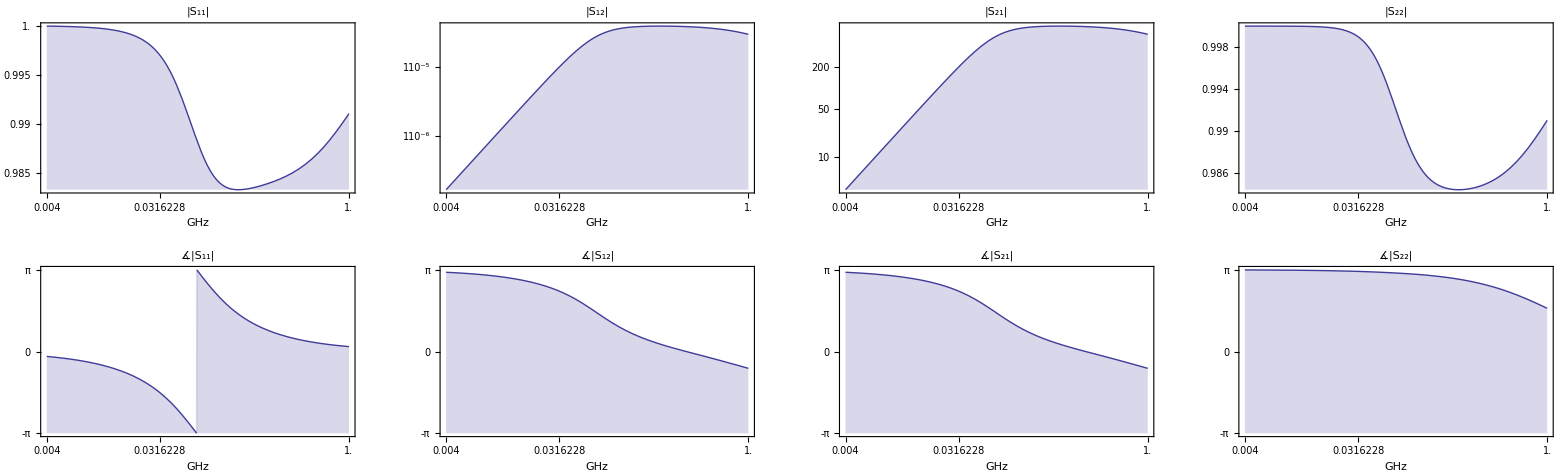

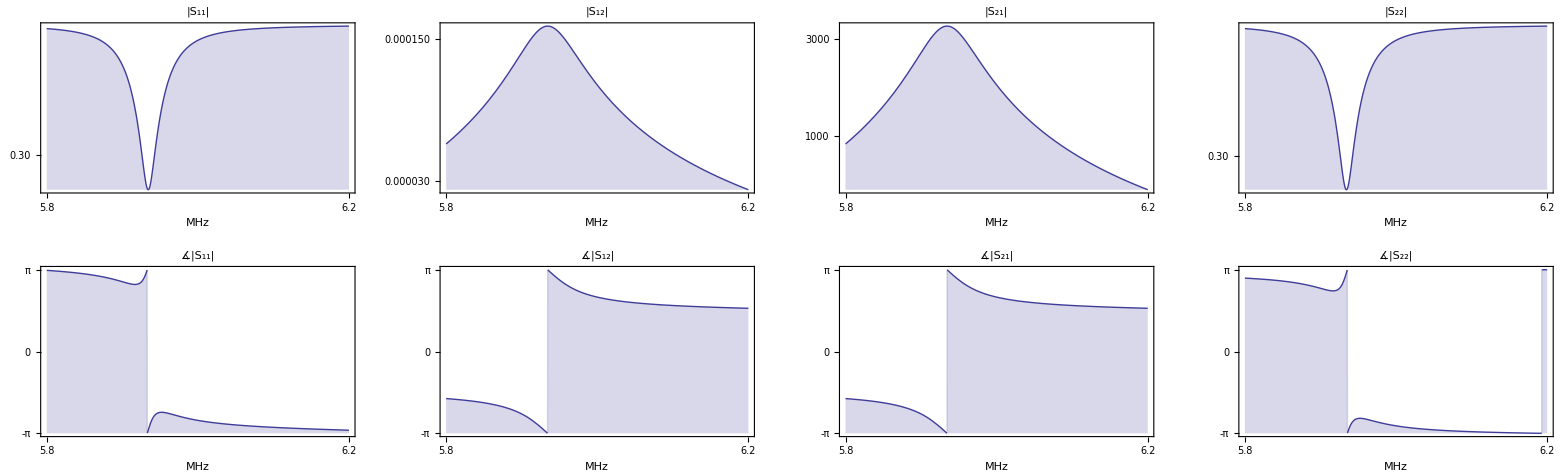

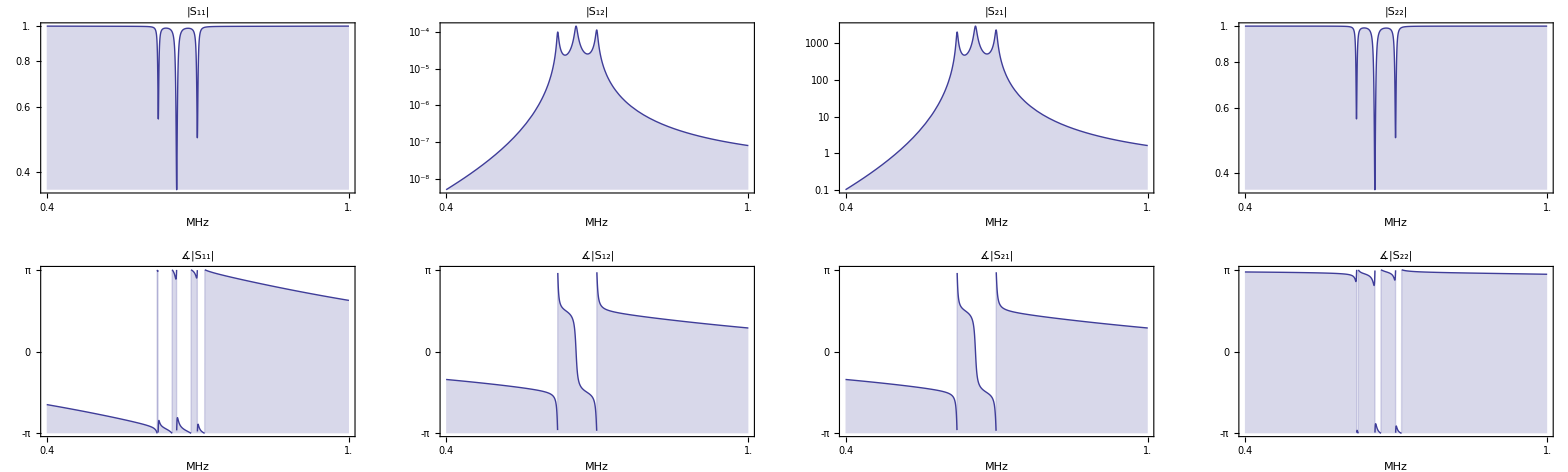

```mathematica
LogLinearPlotSparameters[baseCircuitExpressionSparam/.BasicCircuitParameters,{f,40 10^5,100 10^7}]
LogLinearPlotSparameters[doubleCircuitExpressionSparam/.BasicCircuitParameters,{f,58 10^6,62 10^6}]
LogLinearPlotSparameters[quadCircuitExpressionSparam/.BasicCircuitParameters,{f,40 10^6,100 10^6}]
```

```mathematica
SmithPlot[ToZ[quadCircuitExpression][[1,1]],{f, 40 10^6,100 10^6}]
```

$Aborted

### An inductively coupled resonator

```mathematica
inductivelyCoupledCircuit=CircuitCascade[TwoportSeries[OneportC[c2]],CircuitCascade[TwoportCoupledInductors[OneportL[l2],OneportL[l1],OneportL[m1]],TwoportSeries[OneportC[c1]]]]

CircuitGraphics[inductivelyCoupledCircuit,Frame->False]
```

```mathematica
inductivelyCoupledCircuitExpression=CircuitExpression[inductivelyCoupledCircuit,ω]
```

```mathematica
inductivelyCoupledCircuitSparam=ToS[inductivelyCoupledCircuitExpression,{50.,1}]/.{c2->10^-9,c1->10^-9,l2->10^-11,l1->10^-12,m1->10^0}//Simplify
```

```mathematica
LogLinearPlotSparameters[inductivelyCoupledCircuitSparam,{ω,10 10^3,1 10^5}]
```

### A waveguide

```mathematica
spar=ToS[TwoportWaveguideABCD[z0,β,l]]/.{z0->50ω,β->.1,l->2}
```

```mathematica
LogLinearPlotSparameters[spar,{ω,10^-9,10 10^6}]
```

### A metamaterial (NOT Working yet)

```mathematica
meta=CircuitCascade[CircuitCascade[CircuitCascade[CircuitCascade[CircuitCascade[TwoportSeries[OneportR[r1]],TwoportSeries[OneportL[l1]]],TwoportSeries[OneportC[c1]]],TwoportShunt[OneportR[r2]]],TwoportShunt[OneportL[l2]]],TwoportShunt[OneportC[c2]]]/.{r1->.0001,r2->.0001,l1->10^-12,l2->10^-12,c1->10^-6,c2->10^-6}
CircuitGraphics[meta]
mat=HighpassCircuitExpression=CircuitExpression[meta,ω]
γ=Log[Eigensystem[List@@mat][[1]]]
```

```mathematica
LogLogPlot[Arg[γ[[1]]],{ω,10^(-9),10^15},PlotRange->All,Frame->True]
LogLogPlot[Re[γ[[1]]],{ω,10^(-9),10^15},PlotRange->All,Frame->True]
LogLogPlot[Arg[γ[[2]]],{ω,10^(-9),10^15},PlotRange->All,Frame->True]
LogLogPlot[Re[γ[[2]]],{ω,10^(-9),10^15},PlotRange->All,Frame->True]
```

### A double resonant coil (NOT Working yet)

```mathematica
doubleResonantCircuit=CircuitCascade[CircuitCascade[TwoportShunt[OneportC[c1]] ,TwoportShunt[OneportL[l1]]],TwoportShunt[OneportSeries[OneportL[l2],OneportC[c2]]]]
CircuitGraphics[doubleResonantCircuit]
doubleResonantCircuitExpression=CircuitExpression[doubleResonantCircuit,ω]
MatrixForm[doubleResonantExpression]
doubleResonantCircuitExpressionSparam=ToS[doubleResonantCircuitExpression,{50.,1. 10^7}]//Chop
doubleResonantCircuitParameters={c1->10. 10^-10,l1->.2 10^-6,c2->1. 10^-10,l2->1 10^-6};
```

```mathematica
LogLinearPlotSparameters[doubleResonantCircuitExpressionSparam/.doubleResonantCircuitParameters,{ω,6 10^7, 1.5 10^8}]
```

### Reading (and using) touchstone files

#### List of all available touchstone file examples

```mathematica
SetDirectory["/Users/Jan G. Korvink/Desktop/DT/3 Temp Docs/CircuitTheory/TouchstoneExamples/"]
FileNames[{"*.s*p","*.ts"}]
```

#### Comprehensive touchstone file reading test

```mathematica
SetDirectory["/Users/Jan G. Korvink/Desktop/DT/3 Temp Docs/CircuitTheory/TouchstoneExamples/"]

(ReadTouchstone[StringJoin["/Users/Jan G. Korvink/Desktop/DT/3 Temp Docs/CircuitTheory/TouchstoneExamples/",ToString[#]]]&/@FileNames[{"*.s*p","*.ts"}])
```

#### Plotting a touchstone S-parameter file of a transistor (source: Oliver Gruschke)

```mathematica
PlotSparameters[ExtractTouchstoneNetwork[ReadTouchstone[StringJoin["/Users/Jan G. Korvink/Desktop/DT/3 Temp Docs/CircuitTheory/TouchstoneExamples/","f551432n.s2p"]]],{f, 1.1*^8, 1.7*^10}]
```

### Senn P 76

CircuitCascade[TwoportSeries[OneportC[1.2×10^-12]],CircuitCascade[TwoportSeries[OneportL[13/100000000]],CircuitCascade[TwoportShunt[OneportC[17/250000000000]],TwoportShunt[OneportL[2.4×10^-9]]]]]

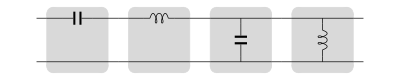

/Users/Jan G. Korvink/Desktop/DT/3 Temp Docs/CircuitTheory/senncircuit1pic.pdf

^A{{(55.1667+0. ⅈ)-1/ω(0.+8.33333×10^11 ⅈ) ((0.+0. ⅈ)-(0.+4.16667×10^8 ⅈ)/ω+(0.+6.8×10^-11 ⅈ) ω)-(8.84×10^-18+0. ⅈ) ω^2,-(0.+8.33333×10^11 ⅈ)/ω+(13 ⅈ ω)/100000000},{(0.+0. ⅈ)-(0.+4.16667×10^8 ⅈ)/ω+(0.+6.8×10^-11 ⅈ) ω,1}}

((55.1667+0. ⅈ)-((0.+8.33333×10^11 ⅈ) ((0.+0. ⅈ)-(0.+4.16667×10^8 ⅈ)/ω+(0.+6.8×10^-11 ⅈ) ω))/ω-(8.84×10^-18+0. ⅈ) ω^2 | -(0.+8.33333×10^11 ⅈ)/ω+(13 ⅈ ω)/100000000
(0.+0. ⅈ)-(0.+4.16667×10^8 ⅈ)/ω+(0.+6.8×10^-11 ⅈ) ω | 1)

^S{{(54.1667+1/50 (-(0.+8.33333×10^11 ⅈ)/ω+(13 ⅈ ω)/100000000)-(3.47222×10^20+0. ⅈ)/ω^2+(0.+2.08333×10^10 ⅈ)/ω)/(56.1667+1/50 (-(0.+8.33333×10^11 ⅈ)/ω+(13 ⅈ ω)/100000000)-(3.47222×10^20+0. ⅈ)/ω^2-(0.+2.08333×10^10 ⅈ)/ω),(2. (55.1667-(3.47222×10^20+0. ⅈ)/ω^2+((0.+4.16667×10^8 ⅈ) (-(0.+8.33333×10^11 ⅈ)/ω+(13 ⅈ ω)/100000000))/ω))/(56.1667+1/50 (-(0.+8.33333×10^11 ⅈ)/ω+(13 ⅈ ω)/100000000)-(3.47222×10^20+0. ⅈ)/ω^2-(0.+2.08333×10^10 ⅈ)/ω)},{2./(56.1667+1/50 (-(0.+8.33333×10^11 ⅈ)/ω+(13 ⅈ ω)/100000000)-(3.47222×10^20+0. ⅈ)/ω^2-(0.+2.08333×10^10 ⅈ)/ω),(-54.1667+1/50 (-(0.+8.33333×10^11 ⅈ)/ω+(13 ⅈ ω)/100000000)+(3.47222×10^20+0. ⅈ)/ω^2+(0.+2.08333×10^10 ⅈ)/ω)/(56.1667+1/50 (-(0.+8.33333×10^11 ⅈ)/ω+(13 ⅈ ω)/100000000)-(3.47222×10^20+0. ⅈ)/ω^2-(0.+2.08333×10^10 ⅈ)/ω)}}

```mathematica
sennCircuit1=CircuitCascade[TwoportSeries[OneportC[1.2 10^-12]],CircuitCascade[TwoportSeries[OneportL[130 10^-9]],CircuitCascade[TwoportShunt[OneportC[68 10^-12]],TwoportShunt[OneportL[2.4 10^-9]]]]]
senncircuit1pic=CircuitGraphics[sennCircuit1]
Export["/Users/Jan G. Korvink/Desktop/DT/3 Temp Docs/CircuitTheory/senncircuit1pic.pdf",senncircuit1pic]
sennCircuit1Expression=CircuitExpression[sennCircuit1,ω]
MatrixForm[sennCircuit1Expression]
sennCircuit1ExpressionSparam=ToS[sennCircuit1Expression,{50.,50}]//Chop
```

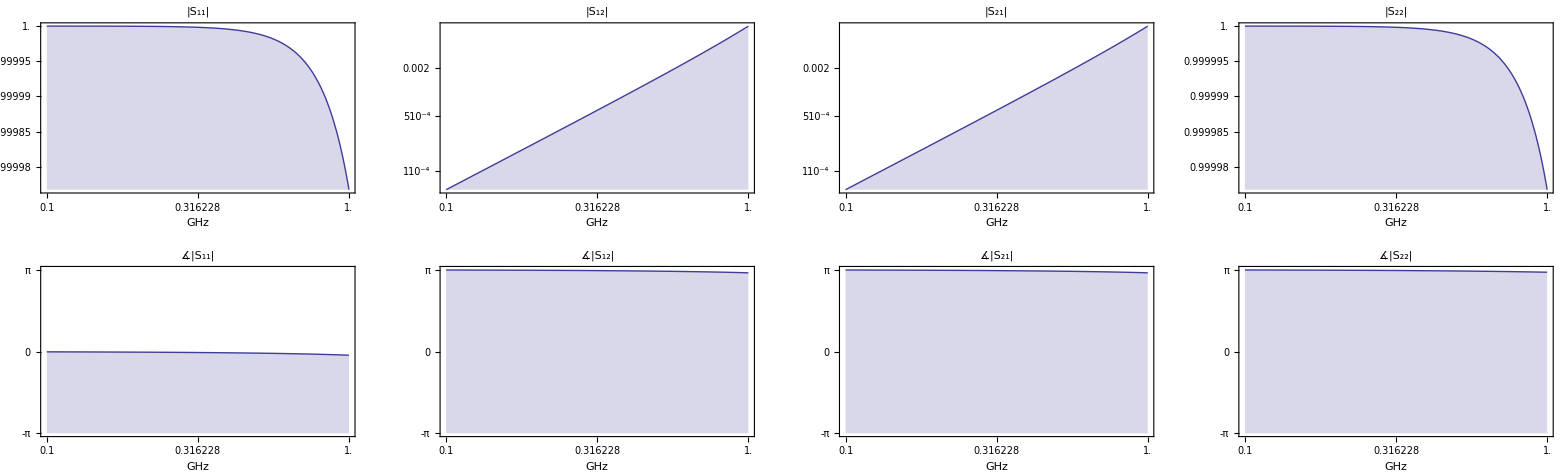

```mathematica
LogLinearPlotSparameters[sennCircuit1ExpressionSparam,{ω,1 10^8, 10 10^8}]
```

```mathematica
ToH[sennCircuit1Expression]
```

^H{{-(0.+8.33333×10^11 ⅈ)/ω+(0.+1.3×10^-7 ⅈ) ω,1.+0. ⅈ},{1,(0.+0. ⅈ)+(0.+4.16667×10^8 ⅈ)/ω-(0.+6.8×10^-11 ⅈ) ω}}

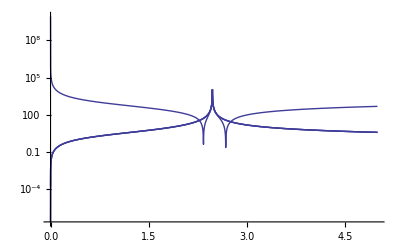

```mathematica
LogPlot[Abs[List@@ToZ[sennCircuit1Expression]],{ω,1 10^0, 5 10^9},PlotRange->All]
```

```mathematica
sennCircuit1
```

CircuitCascade[TwoportSeries[OneportC[1.2×10^-12]],CircuitCascade[TwoportSeries[OneportL[13/100000000]],CircuitCascade[TwoportShunt[OneportC[17/250000000000]],TwoportShunt[OneportL[2.4×10^-9]]]]]

```mathematica
sennCircuit1/.OneportConversionRules[ω]/.TwoportConversionRules
```

CircuitCascade[^A{{1,-(0.+8.33333×10^11 ⅈ)/ω},{0,1}},CircuitCascade[^A{{1,(13 ⅈ ω)/100000000},{0,1}},CircuitCascade[^A{{1,0},{(17 ⅈ ω)/250000000000,1}},^A{{1,0},{-(0.+4.16667×10^8 ⅈ)/ω,1}}]]]

### Senn P 84

CircuitCascade[TwoportShunt[OneportL[1.5×10^-9]],CircuitCascade[TwoportShunt[OneportC[1/10000000000]],CircuitCascade[TwoportSeries[OneportC[6.8×10^-12]],CircuitCascade[TwoportShunt[OneportL[33/1000000000]],TwoportSeries[OneportL[17/250000000]]]]]]

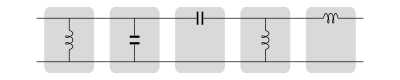

/Users/Jan G. Korvink/Desktop/DT/3 Temp Docs/CircuitTheory/senncircuit5pic.pdf

^A{{1-(4.45633×10^18+0. ⅈ)/ω^2,-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω},{-(0.+4.75936×10^8 ⅈ)/ω-((0.+6.66667×10^8 ⅈ) (1-(4.45633×10^18+0. ⅈ)/ω^2))/ω+(0.+1.×10^-10 ⅈ) ω,(48.0695+0. ⅈ)-((0.+6.66667×10^8 ⅈ) (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω))/ω-(6.8×10^-18+0. ⅈ) ω^2}}

(1-(4.45633×10^18+0. ⅈ)/ω^2 | -(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω
-(0.+4.75936×10^8 ⅈ)/ω-((0.+6.66667×10^8 ⅈ) (1-(4.45633×10^18+0. ⅈ)/ω^2))/ω+(0.+1.×10^-10 ⅈ) ω | (48.0695+0. ⅈ)-((0.+6.66667×10^8 ⅈ) (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω))/ω-(6.8×10^-18+0. ⅈ) ω^2)

^S{{(-47.0695-50 (-(0.+4.75936×10^8 ⅈ)/ω-((0.+6.66667×10^8 ⅈ) (1-(4.45633×10^18)/ω^2))/ω)+1/50 (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω)-(4.45633×10^18)/ω^2+1/ω(0.+6.66667×10^8 ⅈ) (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω))/(49.0695+50 (-(0.+4.75936×10^8 ⅈ)/ω-((0.+6.66667×10^8 ⅈ) (1-(4.45633×10^18)/ω^2))/ω)+1/50 (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω)-(4.45633×10^18)/ω^2-1/ω(0.+6.66667×10^8 ⅈ) (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω)),(0.00447214 ((1-(4.45633×10^18)/ω^2) (48.0695-1/ω(0.+6.66667×10^8 ⅈ) (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω))-(-(0.+4.75936×10^8 ⅈ)/ω-((0.+6.66667×10^8 ⅈ) (1-(4.45633×10^18)/ω^2))/ω) (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω)))/(49.0695+50 (-(0.+4.75936×10^8 ⅈ)/ω-((0.+6.66667×10^8 ⅈ) (1-(4.45633×10^18)/ω^2))/ω)+1/50 (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω)-(4.45633×10^18)/ω^2-1/ω(0.+6.66667×10^8 ⅈ) (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω))},{894.427/(49.0695+50 (-(0.+4.75936×10^8 ⅈ)/ω-((0.+6.66667×10^8 ⅈ) (1-(4.45633×10^18)/ω^2))/ω)+1/50 (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω)-(4.45633×10^18)/ω^2-1/ω(0.+6.66667×10^8 ⅈ) (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω)),(47.0695-50 (-(0.+4.75936×10^8 ⅈ)/ω-((0.+6.66667×10^8 ⅈ) (1-(4.45633×10^18)/ω^2))/ω)+1/50 (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω)+(4.45633×10^18)/ω^2-1/ω(0.+6.66667×10^8 ⅈ) (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω))/(49.0695+50 (-(0.+4.75936×10^8 ⅈ)/ω-((0.+6.66667×10^8 ⅈ) (1-(4.45633×10^18)/ω^2))/ω)+1/50 (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω)-(4.45633×10^18)/ω^2-1/ω(0.+6.66667×10^8 ⅈ) (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω))}}

```mathematica
sennCircuit5=CircuitCascade[TwoportShunt[OneportL[1.5 10^-9]],CircuitCascade[TwoportShunt[OneportC[100 10^-12]],CircuitCascade[TwoportSeries[OneportC[6.8 10^-12]],CircuitCascade[TwoportShunt[OneportL[33 10^-9]],TwoportSeries[OneportL[68 10^-9]]]]]]
senncircuit5pic=CircuitGraphics[sennCircuit5]
Export["/Users/Jan G. Korvink/Desktop/DT/3 Temp Docs/CircuitTheory/senncircuit5pic.pdf",senncircuit5pic]
sennCircuit5Expression=CircuitExpression[sennCircuit5,ω]
MatrixForm[sennCircuit5Expression]
sennCircuit5ExpressionSparam=ToS[sennCircuit5Expression,{50.,1. 10^7}]//Chop
```

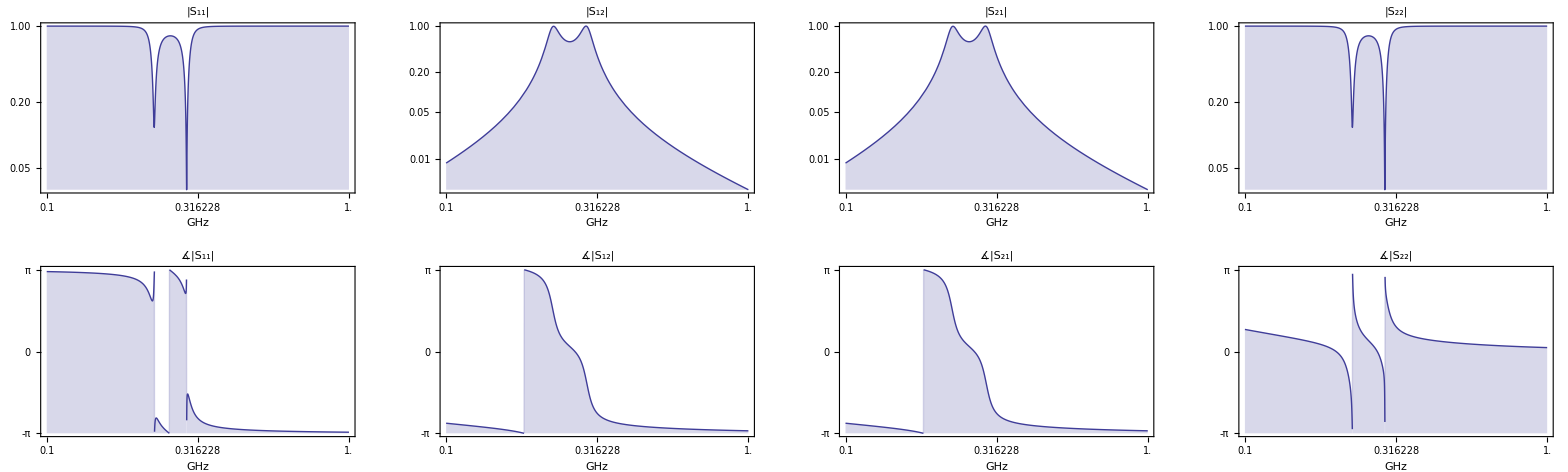

```mathematica
LogLinearPlotSparameters[ToS[sennCircuit5Expression],{ω,1 10^9, 10^10}]
```

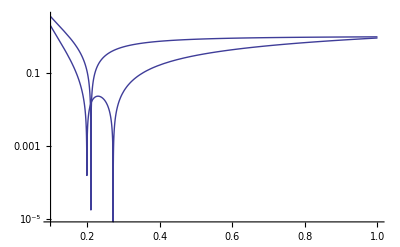

```mathematica
LogPlot[Abs[sennCircuit5Expression.{1,0}],{ω,1 10^9, 10^10},PlotRange->All]
```

```mathematica
ToH[sennCircuit5Expression]
```

^H{{(ω ((0.-4.50089×10^11 ⅈ)+(0.+6.8×10^-8 ⅈ) ω^2))/((-3.00059×10^20+0. ⅈ)+(93.4029+0. ⅈ) ω^2-(6.8×10^-18+0. ⅈ) ω^4),((131072.+0. ⅈ)+(1.+0. ⅈ) ω^2-(7.70372×10^-34+0. ⅈ) ω^4)/((-3.00059×10^20+0. ⅈ)+(93.4029+0. ⅈ) ω^2-(6.8×10^-18+0. ⅈ) ω^4)},{ω^2/((-3.00059×10^20+0. ⅈ)+(93.4029+0. ⅈ) ω^2-(6.8×10^-18+0. ⅈ) ω^4),((0.+2.97089×10^27 ⅈ)-(0.+1.1426×10^9 ⅈ) ω^2+(0.+1.×10^-10 ⅈ) ω^4)/((3.00059×10^20+0. ⅈ) ω-(93.4029+0. ⅈ) ω^3+(6.8×10^-18+0. ⅈ) ω^5)}}

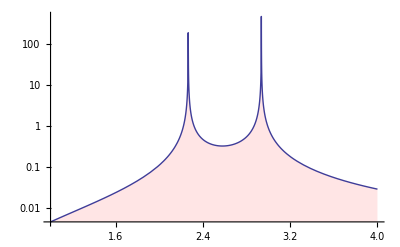

```mathematica
LogPlot[Tooltip[Abs[ToH[sennCircuit5Expression][[1,2]]]],{ω,1 10^9, 4 10^9},PlotRange->All,FillingStyle->{Opacity[.1,Red]},Filling->Bottom]
```

### A cable trap

TwoportSeries[OneportShortedStub[50,π/40,0.00001]]

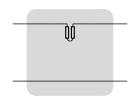

^A{{1,(0.+0.00024674 ⅈ) f},{0,1}}

^S{{((0.+4.9348×10^-6 ⅈ) f)/(2+(0.+4.9348×10^-6 ⅈ) f),(4.47214×10^-8+0. ⅈ)/(2+(0.+4.9348×10^-6 ⅈ) f)},{(8.94427×10^7)/(2+(0.+4.9348×10^-6 ⅈ) f),((0.+4.9348×10^-6 ⅈ) f)/(2+(0.+4.9348×10^-6 ⅈ) f)}}

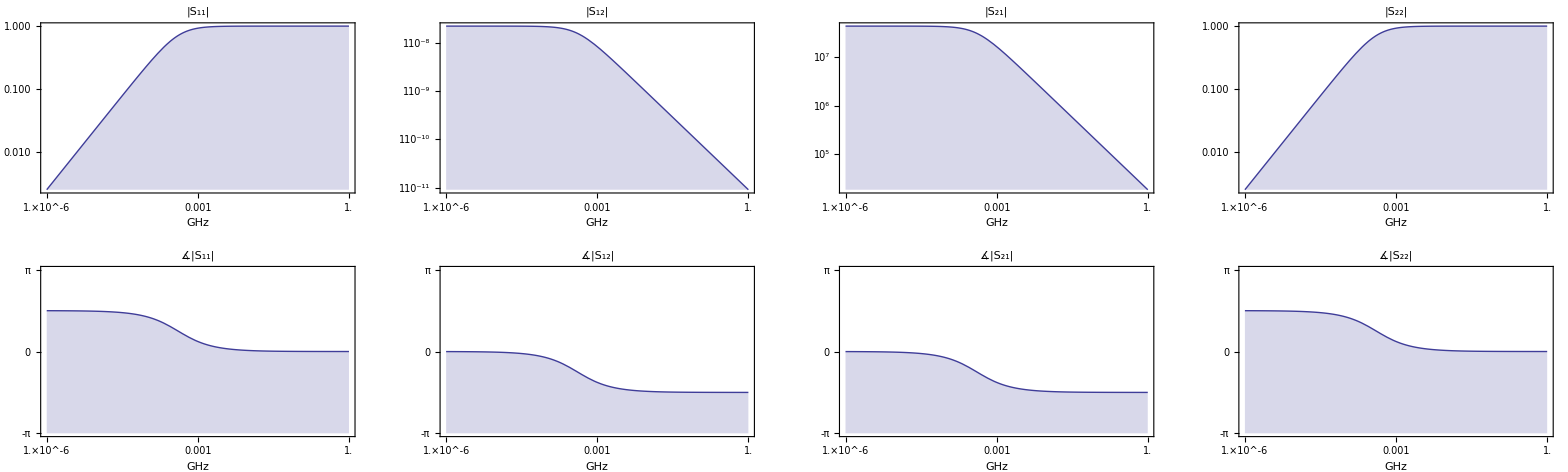

```mathematica
circuit=TwoportSeries[OneportShortedStub[50,π/40,.00001]]
CircuitGraphics[circuit]
expression=CircuitExpression[circuit,2π f]
sparam=ToS[expression,{50.,1. 10^17}]
LogLinearPlotSparameters[sparam,{f, 10^3, 10^9}]
```

TwoportShunt[OneportShortedStub[50,π/40,0.00001]]

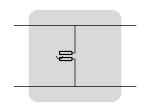

^A{{1,0},{-(0.+4052.85 ⅈ)/f,1}}

^S{{(0.+202642. ⅈ)/((2-(0.+202642. ⅈ)/f) f),(4.47214×10^-8+0. ⅈ)/(2-(0.+202642. ⅈ)/f)},{(8.94427×10^7)/(2-(0.+202642. ⅈ)/f),(0.+202642. ⅈ)/((2-(0.+202642. ⅈ)/f) f)}}

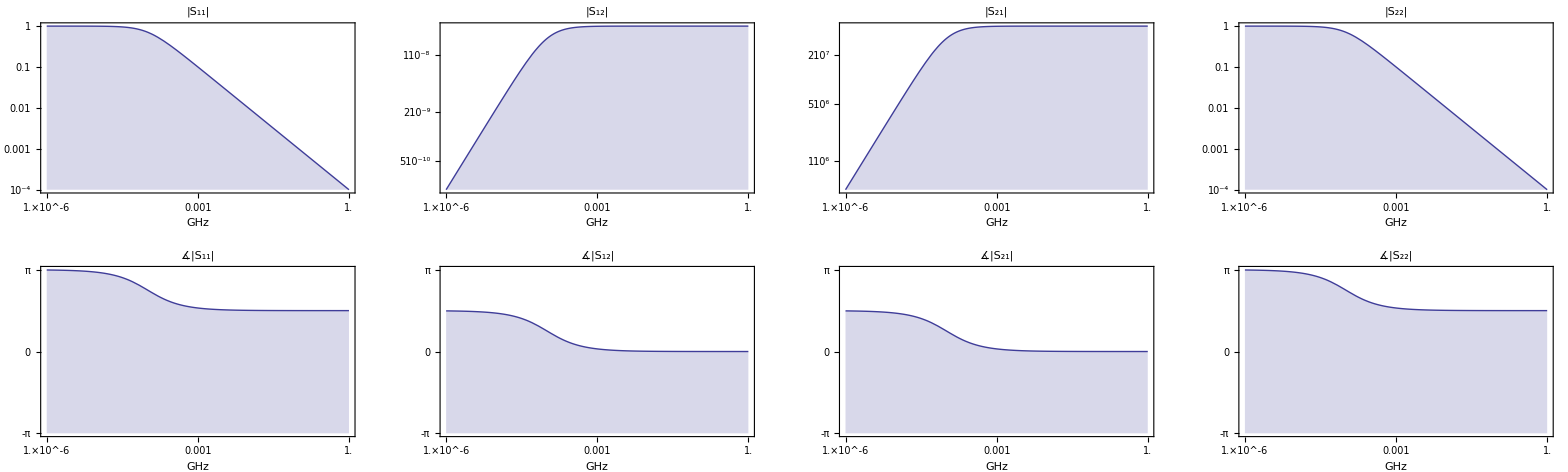

```mathematica
circuit=TwoportShunt[OneportShortedStub[50,π/40,.00001]]
CircuitGraphics[circuit]
expression=CircuitExpression[circuit,2π f]
sparam=ToS[expression,{50.,1. 10^17}]
LogLinearPlotSparameters[sparam,{f, 10^3, 10^9}]
```

### Jan’s current tests

```mathematica
TwoportLossyWaveguideABCD[1,2,3]
TwoportWaveguideABCD[1,2,3]
TwoportBoxsectionABCD[z1,z2]
TwoportCsectionABCD[z1,z2]
TwoportHsectionABCD[z1,z2]
TwoportUnbalancedLadderABCD[z1,z2,3]
```

```mathematica
CircuitGraphics[TwoportShunt[OneportOpenStub[1,1,1]]]
CircuitGraphics[TwoportShunt[OneportShortedStub[1,1,1]]]
```

```mathematica
c=CircuitCascade[CircuitCascade[TwoportSeries[OneportL[1]],TwoportInvert[]],CircuitCascade[TwoportSeries[OneportL[1]],TwoportInvert[]]];
c=TwoportSeries[OneportL[1]];
CircuitGraphics[c]
CircuitExpression[c]
```

```mathematica
TwoportSeriesABCD[ⅈ ω l1]
```

```mathematica
ToZ[ABCD[{a,b},{c,d}]]
```

```mathematica
(ToA[Z@@(List[{0,1},{1,0}].(List@@ToZ[ABCD[{a,b},{c,d}]]).List[{0,1},{1,0}])])
```

```mathematica
/.{a->1,b->ⅈ l1 ω,c->0,d->1}
```

```mathematica
TwoportInvertABCD[]
TwoportSeriesABCD[ⅈ ω l1].TwoportSeriesABCD[ⅈ ω l2]
TwoportSeriesABCD[ⅈ ω l1].TwoportInvertABCD[].TwoportSeriesABCD[ⅈ ω l2].TwoportInvertABCD[]
```

```mathematica
?Circuit*
```

```mathematica
?OneportL
```

```mathematica
Flatten[{{Subscript[z, 11]->zz,Subscript[z, 12]->-zz,Subscript[z, 13]->0,Subscript[z, 14]->0},{Subscript[z, 21]->-zz,Subscript[z, 22]->zz,Subscript[z, 23]->0,Subscript[z, 24]->0},{Subscript[z, 31]->0,Subscript[z, 32]->0,Subscript[z, 33]->∞,Subscript[z, 34]->-∞},{Subscript[z, 41]->0,Subscript[z, 42]->0,Subscript[z, 43]->-∞,Subscript[z, 44]->∞}}]
```

```mathematica
{Subscript[z, 11]->zz,Subscript[z, 12]->-zz,Subscript[z, 13]->0,Subscript[z, 14]->0,Subscript[z, 21]->-zz,Subscript[z, 22]->zz,Subscript[z, 23]->0,Subscript[z, 24]->0,Subscript[z, 31]->0,Subscript[z, 32]->0,Subscript[z, 33]->0,Subscript[z, 34]->0,Subscript[z, 41]->0,Subscript[z, 42]->0,Subscript[z, 43]->-∞,Subscript[z, 44]->∞}
```

```mathematica
Bb={{1,0,-1,0},{0,1,0,-1}};
Cc={{1,0,1,0},{0,1,0,1}};
Z={{Subscript[z, 11],Subscript[z, 12],Subscript[z, 13],Subscript[z, 14]},{Subscript[z, 21],Subscript[z, 22],Subscript[z, 23],Subscript[z, 24]},{Subscript[z, 31],Subscript[z, 32],Subscript[z, 33],Subscript[z, 34]},{Subscript[z, 41],Subscript[z, 42],Subscript[z, 43],Subscript[z, 44]}}
ToA[(Z@@(Bb.Z.PseudoInverse[Cc]//Simplify)/.Flatten[{{Subscript[z, 11]->s,Subscript[z, 12]->-s,Subscript[z, 13]->b,Subscript[z, 14]->b},{Subscript[z, 21]->-s,Subscript[z, 22]->s,Subscript[z, 23]->b,Subscript[z, 24]->b},{Subscript[z, 31]->b,Subscript[z, 32]->b,Subscript[z, 33]->zz,Subscript[z, 34]->-zz},{Subscript[z, 41]->b,Subscript[z, 42]->b,Subscript[z, 43]->-zz,Subscript[z, 44]->zz}}])]/.{s->0}
ToA[(Z@@(Bb.Z.PseudoInverse[Cc]//Simplify)/.Flatten[{{Subscript[z, 11]->zz,Subscript[z, 12]->-zz,Subscript[z, 13]->b,Subscript[z, 14]->b},{Subscript[z, 21]->-zz,Subscript[z, 22]->zz,Subscript[z, 23]->b,Subscript[z, 24]->b},{Subscript[z, 31]->b,Subscript[z, 32]->b,Subscript[z, 33]->s,Subscript[z, 34]->-s},{Subscript[z, 41]->b,Subscript[z, 42]->b,Subscript[z, 43]->-s,Subscript[z, 44]->s}}])]/.{s->0}
```

```mathematica
TwoportSeriesABCD[zz]
```

```mathematica
CircuitGraphics[TwoportSeriesDown[OneportShortedStub[1,1,1]]]
```

```mathematica
Graphics[CircuitGraphics[TwoportSeriesDown[OneportL[1]]]]
```

```mathematica
CircuitExpression[CircuitCascade[TwoportSeries[OneportL[1]],TwoportSeriesDown[OneportL[1]]]]
```

```mathematica
TwoportShuntABCD[OneportL[n]].TwoportSeriesABCD[OneportL[l]].TwoportSeriesDownABCD[OneportL[m]].TwoportShuntABCD[OneportL[n]]
```

```mathematica
OneportL[l]
```

```mathematica
MatrixForm[{{1,0},{0,1}}]
```

(1 | 0
0 | 1)

```mathematica
LongForm[({{1, 0}, {0, 1}})]
```

LongForm[{{1,0},{0,1}}]

```mathematica
?*Form
```

RowBox[{"TableForm", "[", StyleBox["list", "TI"], "]"}] prints with the elements of StyleBox["list", "TI"] arranged in an array of rectangular cells.

```mathematica
?\Left
```

Information::nomatch: No symbol matching "\\Left" found.

### The probehead course example

```mathematica
MRCircuit=CircuitCascade[TwoportShunt[Zc] ,TwoportSeries[Z1],TwoportShunt[Z2],TwoportSeries[Z1]]
MRCircuitExpression=CircuitExpression[MRCircuit,ω];
```

CircuitCascade[TwoportShunt[Zc],TwoportSeries[Z1],TwoportShunt[Z2],TwoportSeries[Z1]]

```mathematica
(List@@MRCircuitExpression)//TeXForm
((MRCircuitExpressionSparam=ToS[MRCircuitExpression,{50.,50}])[[1,1]])//TeXForm
```

\frac{-50
   \left(\frac{\frac{\text{Z1}}{\text{Zc}}+1}{\text{Z2}}+
   \frac{1}{\text{Zc}}\right)-\left(\frac{\text{Z1}}{\tex
   t{Z2}}+1\right)
   \left(\frac{\text{Z1}}{\text{Zc}}+1\right)+\frac{\text
   {Z1}}{\text{Z2}}+\frac{1}{50} \left(\text{Z1}
   \left(\frac{\text{Z1}}{\text{Z2}}+1\right)+\text{Z1}\r
   ight)-\frac{\text{Z1}}{\text{Zc}}+1}{50
   \left(\frac{\frac{\text{Z1}}{\text{Zc}}+1}{\text{Z2}}+
   \frac{1}{\text{Zc}}\right)+\left(\frac{\text{Z1}}{\tex
   t{Z2}}+1\right)
   \left(\frac{\text{Z1}}{\text{Zc}}+1\right)+\frac{\text
   {Z1}}{\text{Z2}}+\frac{1}{50} \left(\text{Z1}
   \left(\frac{\text{Z1}}{\text{Z2}}+1\right)+\text{Z1}\r
   ight)+\frac{\text{Z1}}{\text{Zc}}+1}

```mathematica
(List@@MRCircuitExpression)//TeXForm
((MRCircuitExpressionSparam=ToS[MRCircuitExpression,{50.,50}])[[1,2]])//TeXForm
```

\frac{2. \left(\left(\frac{\text{Z1}}{\text{Z2}}+1\right)
   \left(\left(\frac{\text{Z1}}{\text{Z2}}+1\right)
   \left(\frac{\text{Z1}}{\text{Zc}}+1\right)+\frac{\text
   {Z1}}{\text{Zc}}\right)-\left(\text{Z1}
   \left(\frac{\text{Z1}}{\text{Z2}}+1\right)+\text{Z1}\r
   ight)
   \left(\frac{\frac{\text{Z1}}{\text{Zc}}+1}{\text{Z2}}+
   \frac{1}{\text{Zc}}\right)\right)}{50
   \left(\frac{\frac{\text{Z1}}{\text{Zc}}+1}{\text{Z2}}+
   \frac{1}{\text{Zc}}\right)+\left(\frac{\text{Z1}}{\tex
   t{Z2}}+1\right)
   \left(\frac{\text{Z1}}{\text{Zc}}+1\right)+\frac{\text
   {Z1}}{\text{Z2}}+\frac{1}{50} \left(\text{Z1}
   \left(\frac{\text{Z1}}{\text{Z2}}+1\right)+\text{Z1}\r
   ight)+\frac{\text{Z1}}{\text{Zc}}+1}

CircuitCascade[TwoportShunt[OneportC[c1]],TwoportSeries[OneportL[l1-m]],TwoportShunt[OneportL[m]],TwoportSeries[OneportL[l1-m]]]

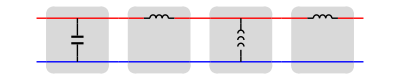

^A{{1+(l1-m)/m,ⅈ (l1-m) ω+ⅈ (1+(l1-m)/m) (l1-m) ω},{ⅈ c1 ω-(ⅈ (1-c1 (l1-m) ω^2))/(m ω),-c1 (l1-m) ω^2+(1+(l1-m)/m) (1-c1 (l1-m) ω^2)}}

(1+(l1-m)/m | ⅈ (l1-m) ω+ⅈ (1+(l1-m)/m) (l1-m) ω
ⅈ c1 ω-(ⅈ (1-c1 (l1-m) ω^2))/(m ω) | -c1 (l1-m) ω^2+(1+(l1-m)/m) (1-c1 (l1-m) ω^2))

```mathematica
MRCircuit=CircuitCascade[TwoportShunt[OneportC[c1]] ,TwoportSeries[OneportL[l1-m]],TwoportShunt[OneportL[m]],TwoportSeries[OneportL[l1-m]]]
mrcircuitpic=CircuitGraphics[MRCircuit]
(*Export["/Users/Jan G. Korvink/Desktop/DT/3 Temp Docs/CircuitTheory/mrcircuitpic.pdf",mrcircuitpic]*)
MRCircuitExpression=CircuitExpression[MRCircuit,ω]
MatrixForm[MRCircuitExpression]
MRCircuitExpressionSparam=ToS[MRCircuitExpression,{50.,50}]//Chop;
MRCircuitParameters={c1->10. 10^-10,l1->.15 10^-7,m->0.01*.15 10^-7};
```

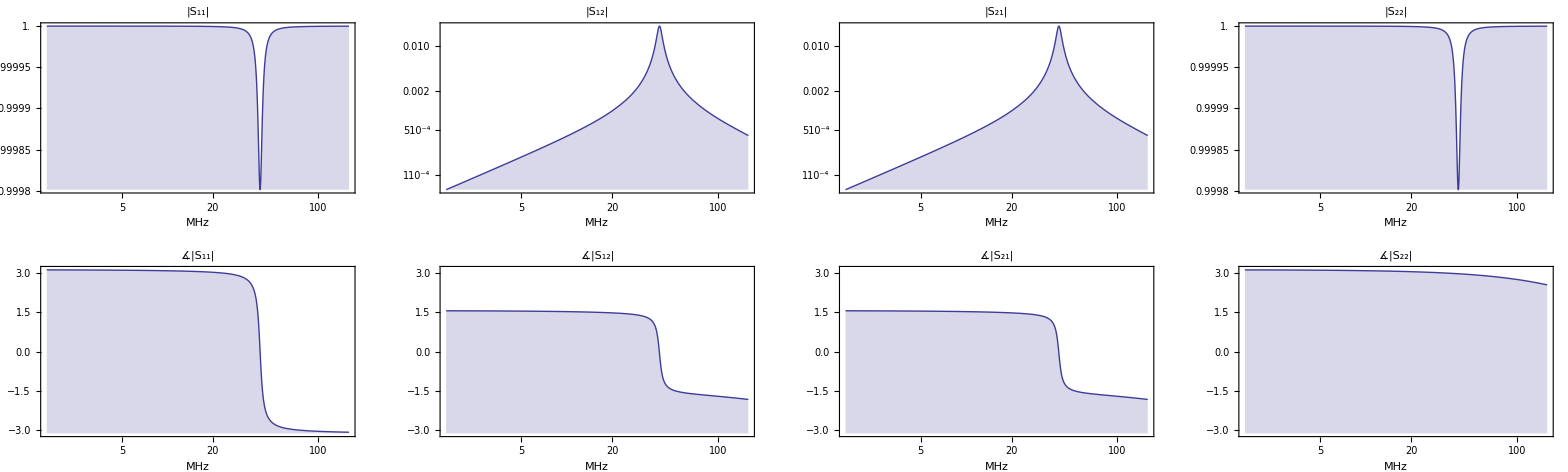

```mathematica
sparamplot=LogLinearPlotSparameters[MRCircuitExpressionSparam/.MRCircuitParameters,{ω,1 10^7, 10^9}]
```

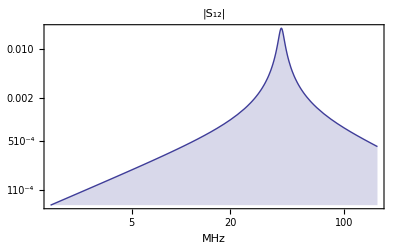

/Users/korvink1/SynchWithVoxalyticCom/KorvinkFiles/3 Temp Docs/S12.pdf

```mathematica
sparamplot[[1,2,1,2,1]]
Export["/Users/korvink1/SynchWithVoxalyticCom/KorvinkFiles/3 Temp Docs/S12.pdf",sparamplot[[1,2,1,2,1]]]
```

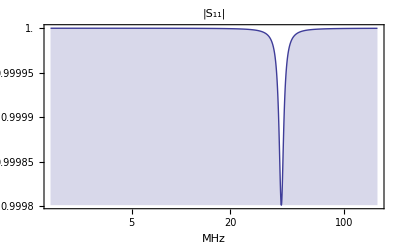

/Users/korvink1/SynchWithVoxalyticCom/KorvinkFiles/3 Temp Docs/S11.pdf

```mathematica
sparamplot[[1,2,1,1,1]]
Export["/Users/korvink1/SynchWithVoxalyticCom/KorvinkFiles/3 Temp Docs/S11.pdf",sparamplot[[1,2,1,1,1]]]
```

```mathematica
(MRCircuitExpressionSparam/.MRCircuitParameters)[[1,2]]
```

(2. (100. (-1.485×10^-17 ω^2+100. (1-1.485×10^-17 ω^2))-(0.+1.49985×10^-6 ⅈ) ω ((0.+1.×10^-9 ⅈ) ω-((0.+6.66667×10^9 ⅈ) (1-1.485×10^-17 ω^2))/ω)))/(100.+(0.+2.9997×10^-8 ⅈ) ω-1.485×10^-17 ω^2+100. (1-1.485×10^-17 ω^2)+50 ((0.+1.×10^-9 ⅈ) ω-((0.+6.66667×10^9 ⅈ) (1-1.485×10^-17 ω^2))/ω))

```mathematica
(MRCircuitExpressionSparam/.MRCircuitParameters)[[1,2]]
```

(2. (100. (-1.485×10^-17 ω^2+100. (1-1.485×10^-17 ω^2))-(0.+1.49985×10^-6 ⅈ) ω ((0.+1.×10^-9 ⅈ) ω-((0.+6.66667×10^9 ⅈ) (1-1.485×10^-17 ω^2))/ω)))/(100.+(0.+2.9997×10^-8 ⅈ) ω-1.485×10^-17 ω^2+100. (1-1.485×10^-17 ω^2)+50 ((0.+1.×10^-9 ⅈ) ω-((0.+6.66667×10^9 ⅈ) (1-1.485×10^-17 ω^2))/ω))

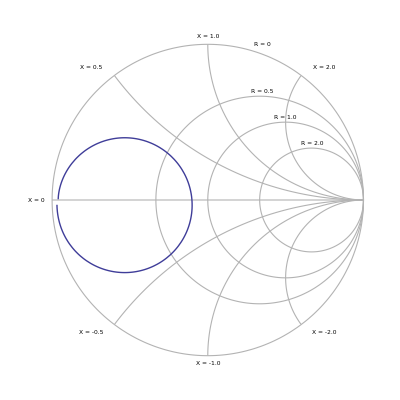

```mathematica
SmithPlot[1+2000(MRCircuitExpressionSparam/.MRCircuitParameters)[[1,2]],{ω,1 10^7, 10^9}]
```

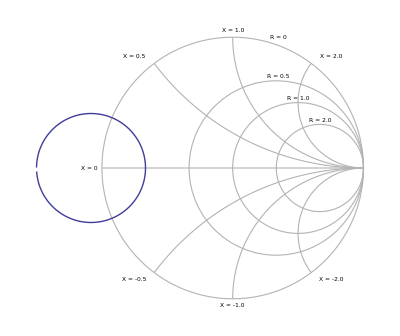

```mathematica
SmithPlot[10(MRCircuitExpressionSparam/.MRCircuitParameters)[[1,1]],{ω,1 10^7, 10^9}]
```

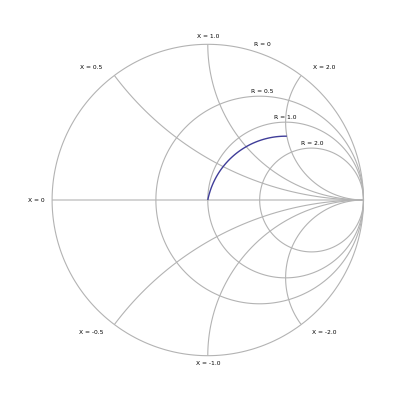

```mathematica
SmithPlot[50+(.2+ⅈ) ω 10^(-9),{ω,1 10^0, 10^11}]
```

### A double resonant probe

```mathematica
doubleResonantCircuit=CircuitCascade[TwoportShunt[OneportC[c2]],TwoportShunt[OneportC[c2]]]
```

CircuitCascade[TwoportShunt[OneportC[c2]],TwoportShunt[OneportC[c2]]]

```mathematica
CircuitGraphics[doubleResonantCircuit]
```

CircuitGraphics[CircuitCascade[TwoportShunt[OneportC[c2]],TwoportShunt[OneportC[c2]]]]

```mathematica
bridgeCircuitExpression=CircuitExpression[doubleResonantCircuit,ω]/.{r1->10000,r2->20000,r3->10000,r4->40000,l1->10^(-9),c1->10^(-12)}
```

^A{{-15/2-110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000),-110000},{-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000),-6}}

```mathematica
bridgeCircuitExpressionSparam=ToS[bridgeCircuitExpression,{50.,1. 10^18}]//Chop
```

^S{{(-4403/2-50 (-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))-110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))/(-4427/2+50 (-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))-110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000)),(1.41421×10^-8 (-6 (-15/2-110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))+110000 (-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))))/(-4427/2+50 (-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))-110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))},{2.82843×10^8/(-4427/2+50 (-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))-110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000)),(-4397/2-50 (-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))+110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))/(-4427/2+50 (-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))-110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))}}

```mathematica
omin=10^10;omax=1 10^11;
LogLinearPlotSparameters[bridgeCircuitExpressionSparam,{ω,omin,omax}]
```

-Graphics-